```mathematica
f1 = w+1/w+1/R^2(X+1/X+U)
s1 = Solve[%==0, w]
```

1/w+w+(U+1/X+X)/R^2

{{w→(-1-U X-X^2-√(-4 R^4 X^2+(1+U X+X^2)^2))/(2 R^2 X)},{w→(-1-U X-X^2+√(-4 R^4 X^2+(1+U X+X^2)^2))/(2 R^2 X)}}

```mathematica
m1 = {Y->-R^2X(w-1/w)}
s2 = Solve[Y==(Y/.m1), w]//Simplify
```

{Y→-R^2 (-1/w+w) X}

{{w→-(Y+√(4 R^4 X^2+Y^2))/(2 R^2 X)},{w→(-Y+√(4 R^4 X^2+Y^2))/(2 R^2 X)}}

```mathematica
Y^2/.m1/.s1//FullSimplify;
If[!Equal@@%,
Print["Not equal"];%, %];
rhs=First[%]
```

(1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X))

```mathematica
Discriminant[rhs, X]//FullSimplify
delt = %/(256 R^8) //Simplify
```

256 R^8 (16 R^8+(-4+U^2)^2-8 R^4 (4+U^2))

16 R^8+(-4+U^2)^2-8 R^4 (4+U^2)

```mathematica
disc0sol = Solve[delt==0, U]//Simplify
```

{{U→2-2 R^2},{U→2 (-1+R^2)},{U→-2 (1+R^2)},{U→2 (1+R^2)}}

```mathematica
(* f_4 on the nodes *)
rhs0 = rhs/.disc0sol//Simplify;
#[[1]]Collect[#[[2]], X]&/@%
```

{(1+X)^2 (1+(2-4 R^2) X+X^2),(-1+X)^2 (1+(-2+4 R^2) X+X^2),(-1+X)^2 (1-2 (1+2 R^2) X+X^2),(1+X)^2 (1+(2+4 R^2) X+X^2)}

```mathematica
(* X0 on the nodes *)
X0 = {-1,1,1,-1};
```

```mathematica
(* initial node parametrization *)
params = {
{X->2(1-2R^2-t)/(t^2-1), Y->(4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->-2(1-2R^2-t)/(t^2-1), Y->(4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->-2(1+2R^2-t)/(t^2-1), Y->(-4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->2(1+2R^2-t)/(t^2-1), Y->(-4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)}
};
```

```mathematica
ClearAll[tvals,tz,sol,sol2];
Do[Module[{rhs1, temp, zsol}, 
Print["----------- n = "<>ToString[n]<>" --------------"];
Print["f_4 = ", Y^2-rhs0[[n]]/.params[[n]]//Simplify];
tvals[n] = Echo[t/.Solve[(X/.params[[n]])==X0[[n]], t]//Simplify];
tz[n] = Echo[First@Solve[z==(t-tvals[n][[1]])/(t-tvals[n][[2]]), t]//Simplify];
temp = {X, w}/.s2/.params[[n]]//ExpandAll//Simplify//PowerExpand//Simplify;
sol2[n] = Echo[First[temp]];
zsol = (temp/.tz[n]//Simplify);
sol[n] = Echo[First[zsol]];
Print["f1 = ",((f1/.disc0sol[[n]])/.{X->#[[1]], w->#[[2]]})&@sol[n]//Simplify];
], {n, 1, 4}]
```

----------- n = 1 --------------

f_4 = 0

{1-2 R,1+2 R}

{t→(-1+z+2 R (1+z))/(-1+z)}

{-(2 (-1+2 R^2+t))/(-1+t^2),((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))}

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

f1 = 0

----------- n = 2 --------------

f_4 = 0

{1-2 R,1+2 R}

{t→(-1+z+2 R (1+z))/(-1+z)}

{(2 (-1+2 R^2+t))/(-1+t^2),-((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))}

{((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),-((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

f1 = 0

----------- n = 3 --------------

f_4 = 0

{1+2 ⅈ R,1-2 ⅈ R}

{t→(-1+z-2 ⅈ R (1+z))/(-1+z)}

{(2 (-1-2 R^2+t))/(-1+t^2),((1+2 R^2-t) (-1+t))/(2 R^2 (1+t))}

{((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))}

f1 = 0

----------- n = 4 --------------

f_4 = 0

{1+2 ⅈ R,1-2 ⅈ R}

{t→(-1+z-2 ⅈ R (1+z))/(-1+z)}

{(2+4 R^2-2 t)/(-1+t^2),-((1+2 R^2-t) (-1+t))/(2 R^2 (1+t))}

{-((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),-((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))}

f1 = 0

```mathematica
ClearAll[getLinearFactorsData];
getLinearFactorsData[expr_,var_]:=Module[{t,num,den,fn,fd,all,linear},(*make sure it's really a single rational expression*)
t=Together[expr];
num=Numerator[t];
den=Denominator[t];
(*factor numerator and denominator in var*)
fn=Rest@FactorList[num];
(*{{factor,exp},...}*)
fd=Rest@FactorList[den];
(*denominator factors get negative exponents*)all=Join[fn,{{#[[1]],-#[[2]]}&/@fd}//Flatten[#,1]&];
(*keep only true linear polynomials in var*)linear=Select[all,PolynomialQ[First[#],var]&&Exponent[First[#],var]==1&];
(*extract exponents and roots*)
{
(*(a) exponents*)
linear[[All,2]],
(*(b) roots:for a z+b==0->z=-b/a*)Simplify[-Coefficient[#[[1]],var,0]/Coefficient[#[[1]],var,1]]&/@linear
}];

(* test *)
expr=-(((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)));
{exponents,roots}=getLinearFactorsData[expr,z];
exponents
roots
ClearAll[expr,exponents,roots]
```

{1,1,-1,-1}

{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}

```mathematica
sol[1]
getLinearFactorsData[Last[%], z]
```

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

#### Cases n = 1, 2

```mathematica
With[{n=1},
Print[sol[n]];
vX = Echo@getLinearFactorsData[First[sol[n]], z];
vw = Echo@getLinearFactorsData[Last[sol[n]], z];
dvec=First[vX];
evec=First[vw];
avec=Last[vX];
bvec=Last[vw];
]
A=1/2/Pi Sum[dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
%/.{BW->Subscript[D,2]}
```

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

(BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])/π

(D_2[(1-R)/(1+R)]-D_2[(-1+R)/(1+R)]-D_2[(1+R)/(1-R)]+D_2[(1+R)/(-1+R)])/π

```mathematica
rules = {{BW[z_]:>BW[1-1/z]},{BW[z_]:>BW[1/(1-z)]},{BW[z_]:>-BW[1/z]},{BW[z_]:>-BW[1-z]},{BW[z_]:>-BW[-z/(1-z)]}}
```

{{BW[z_]:>BW[1-1/z]},{BW[z_]:>BW[1/(1-z)]},{BW[z_]:>-BW[1/z]},{BW[z_]:>-BW[1-z]},{BW[z_]:>-BW[-z/(1-z)]}}

```mathematica
fiveterm[x_,y_] = BW[x]+BW[y]+BW[(1-x)/(1-x y)]+BW[1-x y]+BW[(1-y)/(1-x y)];
```

```mathematica
BW[(1-R)/(1+R)]/.rules//Simplify
```

{BW[(2 R)/(-1+R)],BW[(1+R)/(2 R)],-BW[(1+R)/(1-R)],-BW[(2 R)/(1+R)],-BW[(-1+R)/(2 R)]}

```mathematica
-BW[(-1+R)/(1+R)]/.rules//Simplify
```

{-BW[-2/(-1+R)],-BW[(1+R)/2],BW[(1+R)/(-1+R)],BW[2/(1+R)],BW[1/2-R/2]}

```mathematica
-BW[(1+R)/(1-R)]/.rules//Simplify
```

{-BW[(2 R)/(1+R)],-BW[(-1+R)/(2 R)],BW[(1-R)/(1+R)],BW[(2 R)/(-1+R)],BW[(1+R)/(2 R)]}

```mathematica
BW[(1+R)/(-1+R)]/.rules//Simplify
```

{BW[2/(1+R)],BW[1/2-R/2],-BW[(-1+R)/(1+R)],-BW[-2/(-1+R)],-BW[(1+R)/2]}

```mathematica
A1 = A/.{BW[(1+R)/(1-R)]->-BW[(1-R)/(1+R)], BW[(1+R)/(-1+R)]->-BW[(-1+R)/(1+R)]}//Simplify
```

(2 (BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]))/π

```mathematica
BW[2/(1+R)]/.rules//Simplify
```

{BW[1/2-R/2],BW[(1+R)/(-1+R)],-BW[(1+R)/2],-BW[(-1+R)/(1+R)],-BW[-2/(-1+R)]}

```mathematica
BW[1+R]/.rules//Simplify
```

{BW[R/(1+R)],BW[-1/R],-BW[1/(1+R)],-BW[-R],-BW[1+1/R]}

```mathematica
A
```

(BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])/π

```mathematica
D[PolyLog[2, x], x]
```

-Log[1-x]/x

```mathematica
A/.{BW:>Li2}
D[%, R]//Simplify
%/.{Li2'[x_]:>-Log[1-x]/x}//FullSimplify
Assuming[0<R<1, FullSimplify[%//Simplify]]
```

(Li2[(1-R)/(1+R)]-Li2[(-1+R)/(1+R)]-Li2[(1+R)/(1-R)]+Li2[(1+R)/(-1+R)])/π

-(2 ((-1+R)^2 Li2'[(1-R)/(1+R)]+(-1+R)^2 Li2'[(-1+R)/(1+R)]+(1+R)^2 (Li2'[(1+R)/(1-R)]+Li2'[(1+R)/(-1+R)])))/(π (-1+R^2)^2)

(2 (-2 ArcTanh[(1+R)/(-1+R)]-Log[R]+Log[1/(1+R)]+Log[1+R]))/(π (-1+R^2))

-(2 Log[-R^2])/(π (-1+R^2))

```mathematica
PolyLog[2, -I R]-PolyLog[2, I R]
Assuming[0<R<1, FullSimplify[D[%, R]]]
```

PolyLog[2,-ⅈ R]-PolyLog[2,ⅈ R]

-(2 ⅈ ArcTan[R])/R

```mathematica
PolyLog[2, -R]-PolyLog[2, R]
Assuming[0<R<1, FullSimplify[D[%, R]]]
```

PolyLog[2,-R]-PolyLog[2,R]

Log[-1+2/(1+R)]/R

```mathematica
fiveterm[R, -1]
%/.{BW[-1]->0, BW[2/(1+R)]->-BW[(-1+R)/(1+R)], BW[1+R]->-BW[-R]}
Solve[%==0, BW[(1-R)/(1+R)]]
A2 = A1/.First@%//Simplify
```

BW[-1]+BW[R]+BW[2/(1+R)]+BW[(1-R)/(1+R)]+BW[1+R]

-BW[-R]+BW[R]+BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]

{{BW[(1-R)/(1+R)]→BW[-R]-BW[R]+BW[(-1+R)/(1+R)]}}

(2 (BW[-R]-BW[R]))/π

#### Cases n = 3, 4

```mathematica
With[{n=3},
Print[sol[n]];
vX = Echo@getLinearFactorsData[First[sol[n]], z];
vw = Echo@getLinearFactorsData[Last[sol[n]], z];
dvec=First[vX];
evec=First[vw];
avec=Last[vX];
bvec=Last[vw];
]
A=1/2/Pi Sum[dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
%/.{BW->Subscript[D,2]}
```

{((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))}

{{1,1,-1,-1},{1,(-ⅈ+R)/(ⅈ+R),-1,(ⅈ-R)/(ⅈ+R)}}

{{1,1,-1,-1},{-1,(-ⅈ+R)/(ⅈ+R),1,(ⅈ-R)/(ⅈ+R)}}

(BW[(ⅈ-R)/(ⅈ+R)]-BW[(-ⅈ+R)/(ⅈ+R)]-BW[(ⅈ+R)/(ⅈ-R)]+BW[(ⅈ+R)/(-ⅈ+R)])/π

(D_2[(ⅈ-R)/(ⅈ+R)]-D_2[(-ⅈ+R)/(ⅈ+R)]-D_2[(ⅈ+R)/(ⅈ-R)]+D_2[(ⅈ+R)/(-ⅈ+R)])/π

```mathematica
BW[(ⅈ+R)/(ⅈ-R)]/.rules//Simplify
```

{BW[(2 R)/(ⅈ+R)],BW[(-ⅈ+R)/(2 R)],-BW[(ⅈ-R)/(ⅈ+R)],-BW[(2 R)/(-ⅈ+R)],-BW[(ⅈ+R)/(2 R)]}

```mathematica
BW[(ⅈ+R)/(-ⅈ+R)]/.rules//Simplify
```

{BW[(2 ⅈ)/(ⅈ+R)],BW[1/2+(ⅈ R)/2],-BW[(-ⅈ+R)/(ⅈ+R)],-BW[-(2 ⅈ)/(-ⅈ+R)],-BW[1/2-(ⅈ R)/2]}

```mathematica
A1=A/.{BW[(ⅈ+R)/(ⅈ-R)]->-BW[(ⅈ-R)/(ⅈ+R)], BW[(ⅈ+R)/(-ⅈ+R)]->-BW[(-ⅈ+R)/(ⅈ+R)]}//Simplify
```

(2 (BW[(ⅈ-R)/(ⅈ+R)]-BW[(-ⅈ+R)/(ⅈ+R)]))/π

```mathematica
fiveterm[-I R,-1]//Simplify
```

BW[-1]+BW[1-ⅈ R]+BW[-ⅈ R]+BW[(2 ⅈ)/(ⅈ+R)]+BW[(ⅈ-R)/(ⅈ+R)]

```mathematica
BW[(2 ⅈ)/(ⅈ+R)]/.rules//Simplify
```

{BW[1/2+(ⅈ R)/2],BW[(ⅈ+R)/(-ⅈ+R)],-BW[1/2-(ⅈ R)/2],-BW[(-ⅈ+R)/(ⅈ+R)],-BW[-(2 ⅈ)/(-ⅈ+R)]}

```mathematica
BW[1-ⅈ R]/.rules//Simplify
```

{BW[R/(ⅈ+R)],BW[-ⅈ/R],-BW[1/(1-ⅈ R)],-BW[ⅈ R],-BW[(ⅈ+R)/R]}

```mathematica
fiveterm[-I R,-1]//Simplify
%/.{BW[-1]->0, BW[(2 ⅈ)/(ⅈ+R)]->-BW[(-ⅈ+R)/(ⅈ+R)], BW[1-ⅈ R]->-BW[ⅈ R]}
Solve[%==0, BW[(ⅈ-R)/(ⅈ+R)]]
A2 = A1/.First@%//Simplify
```

BW[-1]+BW[1-ⅈ R]+BW[-ⅈ R]+BW[(2 ⅈ)/(ⅈ+R)]+BW[(ⅈ-R)/(ⅈ+R)]

BW[-ⅈ R]-BW[ⅈ R]+BW[(ⅈ-R)/(ⅈ+R)]-BW[(-ⅈ+R)/(ⅈ+R)]

{{BW[(ⅈ-R)/(ⅈ+R)]→-BW[-ⅈ R]+BW[ⅈ R]+BW[(-ⅈ+R)/(ⅈ+R)]}}

(2 (-BW[-ⅈ R]+BW[ⅈ R]))/π

#### five term derivative

```mathematica
fiveterm[x, y]
D[%, x]//Simplify
%/.{BW'[x_]:>-Log[1-x]/x}//FullSimplify
```

BW[x]+BW[y]+BW[(1-x)/(1-x y)]+BW[(1-y)/(1-x y)]+BW[1-x y]

BW'[x]-y BW'[1-x y]+((-1+y) (BW'[(-1+x)/(-1+x y)]-y BW'[(-1+y)/(-1+x y)]))/(-1+x y)^2

-Log[1-x]/x+((y-x y) Log[x y]-(-1+y) Log[(x (-1+y))/(-1+x y)]+(-1+x) y Log[((-1+x) y)/(-1+x y)])/((-1+x) (-1+x y))

```mathematica
ClearAll[BlochWignerLi2];
BlochWignerLi2[z_]:=Im[PolyLog[2,z]]+Arg[1-z]Log[Abs[z]];
```

#### Sum with omitted terms subtlety

```mathematica
With[{n=1},
Print[sol[n]];
vX = Echo@getLinearFactorsData[First[sol[n]], z];
vw = Echo@getLinearFactorsData[Last[sol[n]], z];
dvec=First[vX];
evec=First[vw];
avec=Last[vX];
bvec=Last[vw];
]
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]],0, dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

(BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])/π

Result is the same as the unrestricted sum

## Full index -- real + imaginary

```mathematica
With[{n=1},
Print[sol[n]];
vX = Echo@getLinearFactorsData[First[sol[n]], z];
vw = Echo@getLinearFactorsData[Last[sol[n]], z];
dvec=First[vX];
evec=First[vw];
avec=Last[vX];
bvec=Last[vw];

{Xat0, wat0} = Echo[sol[n]/.{z->0}//Simplify];
{Xatinf, watinf} = Echo[Limit[sol[n],z->Infinity]//Simplify];
]
A=1/2/Pi Sum[dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
%/.{BW->Subscript[D,2]}
```

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

{-1,1}

{-1,1}

(BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])/π

(D_2[(1-R)/(1+R)]-D_2[(-1+R)/(1+R)]-D_2[(1+R)/(1-R)]+D_2[(1+R)/(-1+R)])/π

```mathematica
B1 = Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;
B2 = Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}];
B = B1 + B2
```

2 Li2[(1-R)/(1+R)]-2 Li2[(-1+R)/(1+R)]-2 Li2[(1+R)/(1-R)]+2 Li2[(1+R)/(-1+R)]+ⅈ Log[-2/(-1+R)] (π+ⅈ Log[(1-R)/(1+R)])+ⅈ Log[2/(1+R)] (π+ⅈ Log[(1-R)/(1+R)])+Log[(2 R)/(-1+R)] Log[(1-R)/(1+R)]-Log[-2/(-1+R)] Log[(-1+R)/(1+R)]-Log[2/(1+R)] Log[(-1+R)/(1+R)]+Log[(2 R)/(-1+R)] (-ⅈ π+Log[(-1+R)/(1+R)])+ⅈ π (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+(-ⅈ π+Log[(-1+R)/(1+R)]) Log[(2 R)/(1+R)]

```mathematica
B1//Expand
```

2 Li2[(1-R)/(1+R)]-2 Li2[(-1+R)/(1+R)]-2 Li2[(1+R)/(1-R)]+2 Li2[(1+R)/(-1+R)]+ⅈ π Log[-2/(-1+R)]-ⅈ π Log[(2 R)/(-1+R)]+ⅈ π Log[2/(1+R)]-Log[-2/(-1+R)] Log[(1-R)/(1+R)]+Log[(2 R)/(-1+R)] Log[(1-R)/(1+R)]-Log[2/(1+R)] Log[(1-R)/(1+R)]-Log[-2/(-1+R)] Log[(-1+R)/(1+R)]+Log[(2 R)/(-1+R)] Log[(-1+R)/(1+R)]-Log[2/(1+R)] Log[(-1+R)/(1+R)]-ⅈ π Log[(2 R)/(1+R)]+Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+Log[(-1+R)/(1+R)] Log[(2 R)/(1+R)]

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[1-z]Log[z]}};
```

```mathematica
Cases[B1, Li2[__], Infinity]
```

{Li2[(1-R)/(1+R)],Li2[(-1+R)/(1+R)],Li2[(1+R)/(1-R)],Li2[(1+R)/(-1+R)]}

```mathematica
Li2[(1+R)/(1-R)]/.Li2Rules/.Li2Rules/.Li2Rules//Simplify//Flatten
Select[%, !FreeQ[#, Li2[(1-R)/(1+R)]]&]
```

{1/6 (-π^2-6 Li2[(1-R)/(1+R)]-6 Log[(-1+R)/(1+R)]^2+3 Log[(1+R)/(-1+R)]^2),1/6 (π^2-6 Li2[(2 R)/(-1+R)]+3 Log[1/2 (-1+1/R)]^2-3 Log[-(2 R)/(-1+R)]^2-6 Log[(2 R)/(-1+R)] Log[(1+R)/(1-R)]),1/2 (-π^2-2 Li2[(1+R)/(2 R)]-Log[(-1+R)/(1+R)]^2+2 Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]-Log[-(1+R)/(2 R)]^2),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),1/6 (π^2-6 Li2[(2 R)/(-1+R)]-3 Log[(-1+R)/(1+R)]^2-6 Log[(2 R)/(-1+R)] Log[(1+R)/(1-R)]+3 Log[(1+R)/(-1+R)]^2),1/2 (π^2-2 Li2[(1+R)/(2 R)]+Log[1/2 (-1+1/R)]^2-2 Log[(2 R)/(-1+R)] Log[(1+R)/(1-R)]-2 Log[(-1+R)/(2 R)] Log[(1+R)/(2 R)]),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),1/6 (π^2-6 Li2[(2 R)/(-1+R)]-6 Log[(2 R)/(-1+R)] Log[(1+R)/(1-R)])}

{1/6 (-π^2-6 Li2[(1-R)/(1+R)]-6 Log[(-1+R)/(1+R)]^2+3 Log[(1+R)/(-1+R)]^2),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2)}

```mathematica
Li2[(1+R)/(-1+R)]/.Li2Rules/.Li2Rules/.Li2Rules//Simplify//Flatten
Select[%, !FreeQ[#, Li2[(R-1)/(1+R)]]&]
```

{1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-6 Log[(1-R)/(1+R)]^2+3 Log[(1+R)/(1-R)]^2),1/6 (π^2-6 Li2[-2/(-1+R)]-3 Log[2/(-1+R)]^2+3 Log[1/2 (-1+R)]^2-6 Log[-2/(-1+R)] Log[(1+R)/(-1+R)]),1/2 (-π^2-2 Li2[(1+R)/2]-Log[1/2 (-1-R)]^2-Log[(1-R)/(1+R)]^2+2 Log[2/(1+R)] Log[(-1+R)/(1+R)]),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2),1/6 (π^2-6 Li2[-2/(-1+R)]-3 Log[(1-R)/(1+R)]^2+3 Log[(1+R)/(1-R)]^2-6 Log[-2/(-1+R)] Log[(1+R)/(-1+R)]),1/2 (π^2-2 Li2[(1+R)/2]+Log[1/2 (-1+R)]^2-2 Log[(1-R)/2] Log[(1+R)/2]-2 Log[-2/(-1+R)] Log[(1+R)/(-1+R)]),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2),1/6 (π^2-6 Li2[-2/(-1+R)]-6 Log[-2/(-1+R)] Log[(1+R)/(-1+R)])}

{1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-6 Log[(1-R)/(1+R)]^2+3 Log[(1+R)/(1-R)]^2),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2)}

```mathematica
ourrules = {
Li2[(1+R)/(1-R)]->1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),
Li2[(1+R)/(-1+R)]->1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2)
}
```

{Li2[(1+R)/(1-R)]→1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),Li2[(1+R)/(-1+R)]→1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2)}

```mathematica
B3 = B1/.ourrules//Simplify
```

4 Li2[(1-R)/(1+R)]-4 Li2[(-1+R)/(1+R)]+ⅈ π Log[1/(1-R)]-ⅈ π Log[R/(-1+R)]+ⅈ π Log[1/(1+R)]-Log[1/(1-R)] Log[(1-R)/(1+R)]+Log[R/(-1+R)] Log[(1-R)/(1+R)]-Log[1/(1+R)] Log[(1-R)/(1+R)]-Log[(1-R)/(1+R)]^2-Log[1/(1-R)] Log[(-1+R)/(1+R)]+Log[R/(-1+R)] Log[(-1+R)/(1+R)]-Log[1/(1+R)] Log[(-1+R)/(1+R)]+Log[(-1+R)/(1+R)]^2-ⅈ π Log[R/(1+R)]+Log[(1-R)/(1+R)] Log[R/(1+R)]+Log[(-1+R)/(1+R)] Log[R/(1+R)]

```mathematica
Li2FiveTerm[x_,y_]:=Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y] - (Pi^2/6-Log[x]Log[1-x]-Log[y]Log[1-y]+Log[(1-x)/(1-x y)]Log[(1-y)/(1-x y)]);
```

```mathematica
Li2FiveTerm[R,-1]
```

-π^2/6+Li2[-1]+Li2[R]+Li2[2/(1+R)]+Li2[(1-R)/(1+R)]+Li2[1+R]+ⅈ π Log[2]+Log[1-R] Log[R]-Log[2/(1+R)] Log[(1-R)/(1+R)]

```mathematica
Li2[2/(1+R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1+R)/2]-3 Log[1/2 (-1-R)]^2),1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)])}

```mathematica
Li2[1+R]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[1/(1+R)]-3 Log[-1/(1+R)]^2),1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])}

```mathematica
ourrules2={Li2[2/(1+R)]->1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]),Li2[1+R]-> 1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])}
```

{Li2[2/(1+R)]→1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]),Li2[1+R]→1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])}

```mathematica
Li2FiveTerm[R,-1]/.ourrules2//Simplify
Solve[%==0, Li2[(1-R)/(1+R)]]
B3/.First[%]/.{Li2[-1]->-π^2/12}//Simplify
(*Assuming[R∈Complexes, FullSimplify[%]]*)
```

π^2/6+Li2[-1]-Li2[-R]+Li2[R]+Li2[(1-R)/(1+R)]-Li2[(-1+R)/(1+R)]+ⅈ π Log[2]+Log[1-R] Log[R]-Log[2/(1+R)] Log[(1-R)/(1+R)]-Log[2/(1+R)] Log[(-1+R)/(1+R)]-Log[-R] Log[1+R]

{{Li2[(1-R)/(1+R)]→1/6 (-π^2-6 Li2[-1]+6 Li2[-R]-6 Li2[R]+6 Li2[(-1+R)/(1+R)]-6 ⅈ π Log[2]-6 Log[1-R] Log[R]+6 Log[2/(1+R)] Log[(1-R)/(1+R)]+6 Log[2/(1+R)] Log[(-1+R)/(1+R)]+6 Log[-R] Log[1+R])}}

-π^2/3+4 Li2[-R]-4 Li2[R]-4 ⅈ π Log[2]+ⅈ π Log[1/(1-R)]-4 Log[1-R] Log[R]-ⅈ π Log[R/(-1+R)]+ⅈ π Log[1/(1+R)]+Log[16] Log[(1-R)/(1+R)]-Log[1/(1-R)] Log[(1-R)/(1+R)]+Log[R/(-1+R)] Log[(1-R)/(1+R)]+3 Log[1/(1+R)] Log[(1-R)/(1+R)]-Log[(1-R)/(1+R)]^2+Log[16] Log[(-1+R)/(1+R)]-Log[1/(1-R)] Log[(-1+R)/(1+R)]+Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+Log[(-1+R)/(1+R)]^2-ⅈ π Log[R/(1+R)]+Log[(1-R)/(1+R)] Log[R/(1+R)]+Log[(-1+R)/(1+R)] Log[R/(1+R)]+4 Log[-R] Log[1+R]

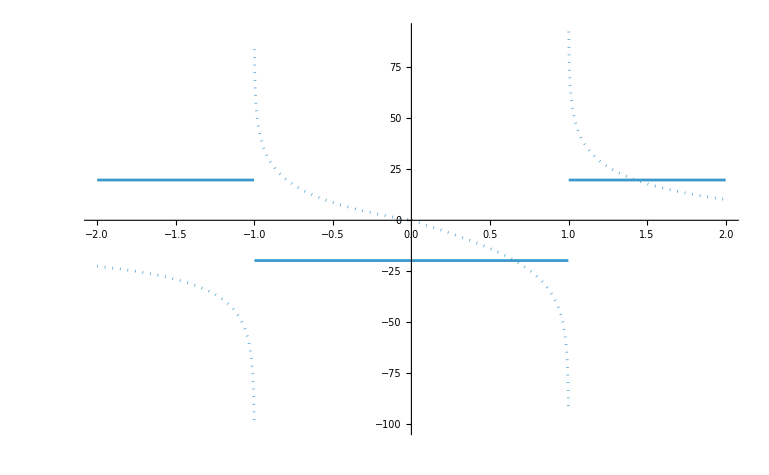

```mathematica
ReImPlot[-2 ⅈ π Log[2]+ⅈ π Log[1/(1-R)]-2 Log[1-R] Log[R]-ⅈ π Log[R/(-1+R)]+ⅈ π Log[1/(1+R)]-ⅈ π Log[(1-R)/(1+R)]-Log[4] Log[(1-R)/(1+R)]-Log[1/(1-R)] Log[(1-R)/(1+R)]+Log[R/(-1+R)] Log[(1-R)/(1+R)]-Log[1/(1+R)] Log[(1-R)/(1+R)]-Log[(1-R)/(1+R)]^2+ⅈ π Log[(-1+R)/(1+R)]+Log[4] Log[(-1+R)/(1+R)]-Log[1/(1-R)] Log[(-1+R)/(1+R)]+Log[R/(-1+R)] Log[(-1+R)/(1+R)]+Log[1/(1+R)] Log[(-1+R)/(1+R)]+Log[(-1+R)/(1+R)]^2-ⅈ π Log[R/(1+R)]-Log[(1-R)/(1+R)] Log[R/(1+R)]+Log[(-1+R)/(1+R)] Log[R/(1+R)]+2 Log[-R] Log[1+R], {R, -2, 2}]
```

```mathematica
PolyLog[2, -1]
```

-π^2/12

#### Derivative check

```mathematica
D[B, R]//Simplify
%/.{Li2'[x_]:>-Log[1-x]/x}//Simplify
Assuming[0<R<1, FullSimplify[PowerExpand[%]]]
```

1/(R (-1+R^2)^2)2 (-ⅈ π+2 ⅈ π R^2-ⅈ π R^4+2 R Log[-2/(-1+R)]-2 R^3 Log[-2/(-1+R)]-2 R Log[(2 R)/(-1+R)]+2 R^3 Log[(2 R)/(-1+R)]+2 R Log[2/(1+R)]-2 R^3 Log[2/(1+R)]+Log[(1-R)/(1+R)]-2 R^2 Log[(1-R)/(1+R)]+R^4 Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)]-2 R^2 Log[(-1+R)/(1+R)]+R^4 Log[(-1+R)/(1+R)]-2 R Log[(2 R)/(1+R)]+2 R^3 Log[(2 R)/(1+R)]-2 (-1+R)^2 R Li2'[(1-R)/(1+R)]-2 (-1+R)^2 R Li2'[(-1+R)/(1+R)]-2 R Li2'[(1+R)/(1-R)]-4 R^2 Li2'[(1+R)/(1-R)]-2 R^3 Li2'[(1+R)/(1-R)]-2 R Li2'[(1+R)/(-1+R)]-4 R^2 Li2'[(1+R)/(-1+R)]-2 R^3 Li2'[(1+R)/(-1+R)])

(2 (-ⅈ π+Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)]))/R

(4 Log[-1+2/(1+R)])/R

```mathematica
B/.{R->2}//Simplify
```

-2 (Li2[-3]-Li2[-1/3]+Li2[1/3]-Li2[3]-ⅈ π Log[3]+Log[4/3] Log[3]+Log[3/2] Log[3]-Log[2] Log[3]+Log[3] Log[4])

```mathematica
B1 = B/.{Li2[z_]:>PolyLog[2, z]}//Simplify
```

ⅈ Log[-2/(-1+R)] (π+ⅈ Log[(1-R)/(1+R)])+ⅈ Log[2/(1+R)] (π+ⅈ Log[(1-R)/(1+R)])+Log[(2 R)/(-1+R)] Log[(1-R)/(1+R)]-Log[-2/(-1+R)] Log[(-1+R)/(1+R)]-Log[2/(1+R)] Log[(-1+R)/(1+R)]+Log[(2 R)/(-1+R)] (-ⅈ π+Log[(-1+R)/(1+R)])+ⅈ π (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+(-ⅈ π+Log[(-1+R)/(1+R)]) Log[(2 R)/(1+R)]+2 PolyLog[2,(1-R)/(1+R)]-2 PolyLog[2,(-1+R)/(1+R)]-2 PolyLog[2,(1+R)/(1-R)]+2 PolyLog[2,(1+R)/(-1+R)]

```mathematica
Plot3D[Evaluate[Re[(4(PolyLog[2, -(R1+I R2)]-PolyLog[2, (R1+I R2)])-(B1/.{R->(R1+I R2)}))/Pi^2]], {R1, -2, 2}, {R2, -2, 2}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[Im[(4(PolyLog[2, -(R1+I R2)]-PolyLog[2, (R1+I R2)])-(B1/.{R->(R1+I R2)}))/Pi^2]], {R1, -2, 2}, {R2, -2, 2}]
```

-Graphics3D-

```mathematica
B/.{R->I}
%/.{Li2[z_]:>PolyLog[2, z]}//Simplify
```

-2 π^2+4 Li2[-ⅈ]-4 Li2[ⅈ]

-2 (4 ⅈ Catalan+π^2)

```mathematica
B
```

2 Li2[(1-R)/(1+R)]-2 Li2[(-1+R)/(1+R)]-2 Li2[(1+R)/(1-R)]+2 Li2[(1+R)/(-1+R)]+ⅈ Log[-2/(-1+R)] (π+ⅈ Log[(1-R)/(1+R)])+ⅈ Log[2/(1+R)] (π+ⅈ Log[(1-R)/(1+R)])+Log[(2 R)/(-1+R)] Log[(1-R)/(1+R)]-Log[-2/(-1+R)] Log[(-1+R)/(1+R)]-Log[2/(1+R)] Log[(-1+R)/(1+R)]+Log[(2 R)/(-1+R)] (-ⅈ π+Log[(-1+R)/(1+R)])+ⅈ π (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+(-ⅈ π+Log[(-1+R)/(1+R)]) Log[(2 R)/(1+R)]

```mathematica
4(PolyLog[2, -R]-PolyLog[2, R])/.{R->I}//FullSimplify
```

-8 ⅈ Catalan

```mathematica
4(PolyLog[2, -I R]-PolyLog[2, I R])/.{R->I}//FullSimplify
```

π^2

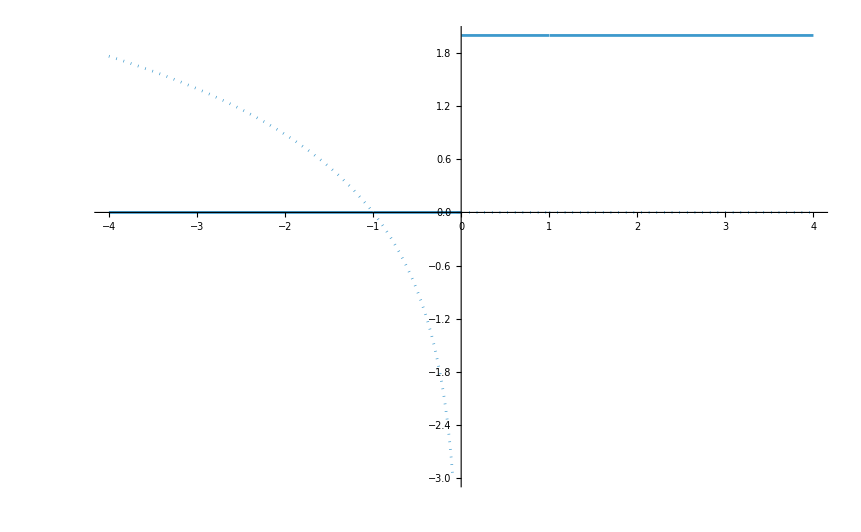

```mathematica
ReImPlot[Evaluate[(4(PolyLog[2, -I R]-PolyLog[2, I R])-(B1/.{R->I R}))/Pi^2], {R, -4, 4}]
```

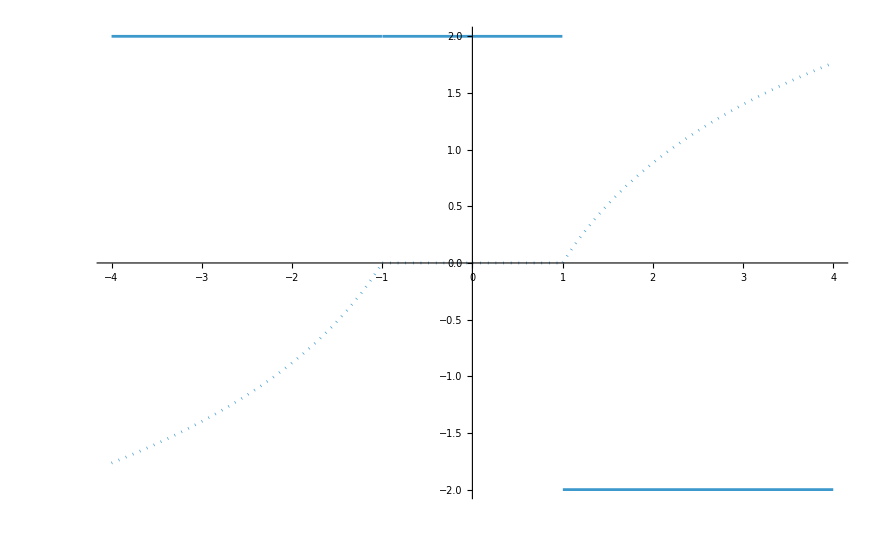

```mathematica
ReImPlot[(4(PolyLog[2, -R]-PolyLog[2, R])-B1)/Pi^2, {R, -4, 4}]
```

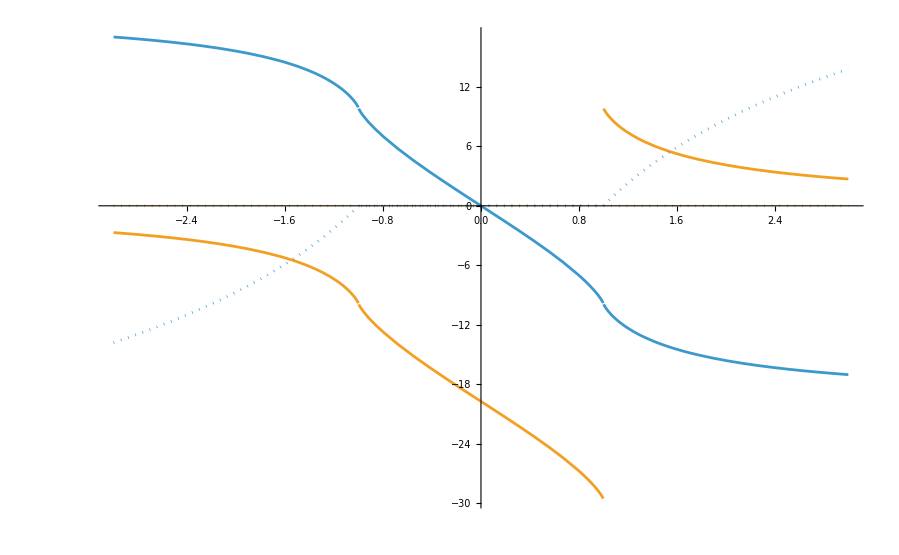

```mathematica
ReImPlot[{4(PolyLog[2, -R]-PolyLog[2, R]), B1}, {R, -3, 3}]
```

```mathematica
PolyLog[2, -R]-PolyLog[2, R]
Assuming[0<R<1, FullSimplify[D[%, R]]]
```

PolyLog[2,-R]-PolyLog[2,R]

Log[-1+2/(1+R)]/R

```mathematica
Sum[dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Logi[avec[[j]]]-Logi[bvec[[k]]])Logi[1-avec[[j]]/bvec[[k]]]),{j,Length[dvec]},{k,Length[evec]}]//FullSimplify
```

-2 Li2[(-1+R)/(1+R)]-2 Li2[(1+R)/(1-R)]+2 Li2[(1+R)/(-1+R)]+2 Li2[-1+2/(1+R)]+(Logi[-2/(-1+R)]-Logi[(2 R)/(-1+R)]+Logi[2/(1+R)]-Logi[(2 R)/(1+R)]) (Logi[-1]+Logi[1]-Logi[(-1+R)/(1+R)]-Logi[-1+2/(1+R)])

```mathematica
Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify
```

ⅈ π (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])

## Convertic quartic to Weierstrass

```mathematica
(x+c)^4(Y^2-rhs)/.{X->a+b/(x+c),Y->y/(x+c)^2}//Expand//Simplify;
ser1 = Series[%, {x, 0, 100}]
```

(-b^4-2 b^3 c (2 a+U)-b^2 c^2 (2+6 a^2-4 R^4+6 a U+U^2)-2 b c^3 (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-c^4 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))+y^2)+(-2 b^3 (2 a+U)-2 b^2 c (2+6 a^2-4 R^4+6 a U+U^2)-6 b c^2 (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-4 c^3 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x+(-b^2 (2+6 a^2-4 R^4+6 a U+U^2)-6 b c (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-6 c^2 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x^2+(-2 b (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-4 c (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x^3+(-1-2 a^2-a^4+4 a^2 R^4-2 a U-2 a^3 U-a^2 U^2) x^4+O[x]^101

```mathematica
sol1 = Solve[Coefficient[ser1, x^4]==0, a]
```

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2))}}

```mathematica
Coefficient[ser1, x^3]/.sol1//FullSimplify
First@Solve[#==-4, b]&/@%//FullSimplify;
sol2 = MapThread[Join, {sol1, %}]
```

{-2 b R^2 (-4-(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))),-2 b R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2))),2 b R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))),2 b R^2 (-4-(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))}

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2)),b→-2/(R^2 (4+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2)),b→2/(R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2)),b→-2/(R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2)),b→2/(R^2 (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2))))}}

```mathematica
Coefficient[ser1, x^2]/.sol2//FullSimplify;
First@Solve[#==0, c]&/@%//FullSimplify;
sol3 = MapThread[Join, {sol2, %}]
```

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2)),b→-2/(R^2 (4+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2)))),c→-(4-8 R^4-U^2+6 R^2 (U+√(-4+(-2 R^2+U)^2)))/(6 R^4 (-4+(-2 R^2+U)^2) (2+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2)),b→2/(R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))),c→(16 R^8-8 R^6 (2 U+√(-4+(-2 R^2+U)^2))+4 R^4 (-4+U √(-4+(-2 R^2+U)^2))-(-2+U) (2+U) (-2+U (U+√(-4+(-2 R^2+U)^2)))+2 R^2 (2 √(-4+(-2 R^2+U)^2)+U (-2+U (2 U+√(-4+(-2 R^2+U)^2)))))/(24 R^4 (-4+(-2 R^2+U)^2))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2)),b→-2/(R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))),c→-(-4+8 R^4+U^2+6 R^2 (U+√(-4+(2 R^2+U)^2)))/(6 R^4 (-4+(2 R^2+U)^2) (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2)),b→2/(R^2 (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))),c→(16 R^8+8 R^6 (2 U+√(-4+(2 R^2+U)^2))+4 R^4 (-4+U √(-4+(2 R^2+U)^2))-(-2+U) (2+U) (-2+U (U+√(-4+(2 R^2+U)^2)))-2 R^2 (2 √(-4+(2 R^2+U)^2)+U (-2+U (2 U+√(-4+(2 R^2+U)^2)))))/(24 R^4 (-4+(2 R^2+U)^2))}}

```mathematica
Coefficient[ser1, x]/.sol3[[1]]//FullSimplify//PowerExpand
```

(8 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)) (-4-(2 R^2-U) (-32 R^10+5 √(-4+(-2 R^2+U)^2)+16 R^8 (5 U+√(-4+(-2 R^2+U)^2))-8 R^6 (-7+10 U^2+4 U √(-4+(-2 R^2+U)^2))+4 R^4 (-5 √(-4+(-2 R^2+U)^2)+U (-21+10 U^2+6 U √(-4+(-2 R^2+U)^2)))-2 R^2 (13+U (-10 √(-4+(-2 R^2+U)^2)+U (-21+5 U^2+4 U √(-4+(-2 R^2+U)^2))))+U (13+U (-5 √(-4+(-2 R^2+U)^2)+U (-7+U (U+√(-4+(-2 R^2+U)^2))))))))/(3 R^8 (-4+(-2 R^2+U)^2) (8+6 (2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))+(-2 R^2+U)^2 (-2 R^2+U+√(-4+(-2 R^2+U)^2))^2)^3)

```mathematica
Series[Normal[ser1]/.{x->x+c}, {x, 0, 100}];
(%/.{x->0,y->0})/.sol3//FullSimplify
```

{(32 (114688 R^24-8192 R^22 (69 U+7 √(-4+(-2 R^2+U)^2))+1024 R^20 (-336+1227 U^2+248 U √(-4+(-2 R^2+U)^2))-512 R^18 (-280 √(-4+(-2 R^2+U)^2)+U (-2652+3242 U^2+979 U √(-4+(-2 R^2+U)^2)))+256 R^16 (1425+U (-1932 √(-4+(-2 R^2+U)^2)+U (-9186+5643 U^2+2263 U √(-4+(-2 R^2+U)^2))))-(-4+U^2)^3 (-2+U (-3+U^2) (-√(-4+(-2 R^2+U)^2)+U (-3+U (U+√(-4+(-2 R^2+U)^2)))))+2 R^2 (-4+U^2)^3 (3 √(-4+(-2 R^2+U)^2)+U (18+U (-12 √(-4+(-2 R^2+U)^2)+U (-24+6 U^2+5 U √(-4+(-2 R^2+U)^2)))))-128 R^14 (921 √(-4+(-2 R^2+U)^2)+2 U (4221+2 U (-1434 √(-4+(-2 R^2+U)^2)+U (-4563+1692 U^2+845 U √(-4+(-2 R^2+U)^2)))))+64 R^12 (-2440+U (4545 √(-4+(-2 R^2+U)^2)+2 U (10443+U (-4754 √(-4+(-2 R^2+U)^2)+7 U (-1626+405 U^2+242 U √(-4+(-2 R^2+U)^2))))))-32 R^10 (-1046 √(-4+(-2 R^2+U)^2)+U (-9516+U (8979 √(-4+(-2 R^2+U)^2)+2 U (13773+U (-4752 √(-4+(-2 R^2+U)^2)+7 U (-1302+234 U^2+163 U √(-4+(-2 R^2+U)^2)))))))+16 R^8 (1194+U (-2974 √(-4+(-2 R^2+U)^2)+U (-13542+U (8787 √(-4+(-2 R^2+U)^2)+2 U (10080+U (-2850 √(-4+(-2 R^2+U)^2)+U (-4536+621 U^2+497 U √(-4+(-2 R^2+U)^2))))))))+4 R^4 (-4+U^2) (-102+U (102 √(-4+(-2 R^2+U)^2)+U (264+U (-√(-4+(-2 R^2+U)^2)+U (-6+U (-76 √(-4+(-2 R^2+U)^2)+U (-72+5 U (3 U+4 √(-4+(-2 R^2+U)^2)))))))))-8 R^6 (104 √(-4+(-2 R^2+U)^2)+U (1596+U (-2462 √(-4+(-2 R^2+U)^2)+U (-7468+U (4023 √(-4+(-2 R^2+U)^2)+2 U (3615+2 U (-458 √(-4+(-2 R^2+U)^2)+U (-609+67 U^2+62 U √(-4+(-2 R^2+U)^2)))))))))))/(27 R^12 (-4+(-2 R^2+U)^2) (8+6 (2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))+(-2 R^2+U)^2 (-2 R^2+U+√(-4+(-2 R^2+U)^2))^2)^4),(2 (256 R^16-128 R^14 (2 U+√(-4+(-2 R^2+U)^2))+2 R^2 (-4+U^2)^3 (2 U+√(-4+(-2 R^2+U)^2))+96 R^10 (2+U^2) (2 U+√(-4+(-2 R^2+U)^2))+64 R^12 (-8+U (-2 U+√(-4+(-2 R^2+U)^2)))-(-4+U^2)^3 (-2+U (U+√(-4+(-2 R^2+U)^2)))-24 R^6 (-8 √(-4+(-2 R^2+U)^2)+U (20+U (-2+U^2) (2 U+√(-4+(-2 R^2+U)^2))))-48 R^8 (-14+U (2 √(-4+(-2 R^2+U)^2)+U (2+U √(-4+(-2 R^2+U)^2))))+4 R^4 (-4+U^2) (26+U (6 √(-4+(-2 R^2+U)^2)+U (8+2 U^2+3 U √(-4+(-2 R^2+U)^2))))))/(27 R^12 (-4+(-2 R^2+U)^2) (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))^4),(32 (114688 R^24+8192 R^22 (69 U+7 √(-4+(2 R^2+U)^2))+1024 R^20 (-336+1227 U^2+248 U √(-4+(2 R^2+U)^2))+512 R^18 (-280 √(-4+(2 R^2+U)^2)+U (-2652+3242 U^2+979 U √(-4+(2 R^2+U)^2)))+256 R^16 (1425+U (-1932 √(-4+(2 R^2+U)^2)+U (-9186+5643 U^2+2263 U √(-4+(2 R^2+U)^2))))-(-4+U^2)^3 (-2+U (-3+U^2) (-√(-4+(2 R^2+U)^2)+U (-3+U (U+√(-4+(2 R^2+U)^2)))))-2 R^2 (-4+U^2)^3 (3 √(-4+(2 R^2+U)^2)+U (18+U (-12 √(-4+(2 R^2+U)^2)+U (-24+6 U^2+5 U √(-4+(2 R^2+U)^2)))))+128 R^14 (921 √(-4+(2 R^2+U)^2)+2 U (4221+2 U (-1434 √(-4+(2 R^2+U)^2)+U (-4563+1692 U^2+845 U √(-4+(2 R^2+U)^2)))))+64 R^12 (-2440+U (4545 √(-4+(2 R^2+U)^2)+2 U (10443+U (-4754 √(-4+(2 R^2+U)^2)+7 U (-1626+405 U^2+242 U √(-4+(2 R^2+U)^2))))))+32 R^10 (-1046 √(-4+(2 R^2+U)^2)+U (-9516+U (8979 √(-4+(2 R^2+U)^2)+2 U (13773+U (-4752 √(-4+(2 R^2+U)^2)+7 U (-1302+234 U^2+163 U √(-4+(2 R^2+U)^2)))))))+16 R^8 (1194+U (-2974 √(-4+(2 R^2+U)^2)+U (-13542+U (8787 √(-4+(2 R^2+U)^2)+2 U (10080+U (-2850 √(-4+(2 R^2+U)^2)+U (-4536+621 U^2+497 U √(-4+(2 R^2+U)^2))))))))+4 R^4 (-4+U^2) (-102+U (102 √(-4+(2 R^2+U)^2)+U (264+U (-√(-4+(2 R^2+U)^2)+U (-6+U (-76 √(-4+(2 R^2+U)^2)+U (-72+5 U (3 U+4 √(-4+(2 R^2+U)^2)))))))))+8 R^6 (104 √(-4+(2 R^2+U)^2)+U (1596+U (-2462 √(-4+(2 R^2+U)^2)+U (-7468+U (4023 √(-4+(2 R^2+U)^2)+2 U (3615+2 U (-458 √(-4+(2 R^2+U)^2)+U (-609+67 U^2+62 U √(-4+(2 R^2+U)^2)))))))))))/(27 R^12 (-4+(2 R^2+U)^2) (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^4 (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^4),(2 (256 R^16+128 R^14 (2 U+√(-4+(2 R^2+U)^2))-2 R^2 (-4+U^2)^3 (2 U+√(-4+(2 R^2+U)^2))-96 R^10 (2+U^2) (2 U+√(-4+(2 R^2+U)^2))+64 R^12 (-8+U (-2 U+√(-4+(2 R^2+U)^2)))-(-4+U^2)^3 (-2+U (U+√(-4+(2 R^2+U)^2)))+24 R^6 (-8 √(-4+(2 R^2+U)^2)+U (20+U (-2+U^2) (2 U+√(-4+(2 R^2+U)^2))))-48 R^8 (-14+U (2 √(-4+(2 R^2+U)^2)+U (2+U √(-4+(2 R^2+U)^2))))+4 R^4 (-4+U^2) (26+U (6 √(-4+(2 R^2+U)^2)+U (8+2 U^2+3 U √(-4+(2 R^2+U)^2))))))/(27 R^12 (-4+(2 R^2+U)^2) (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))^4)}

```mathematica
Series[Normal[ser1]/.{x->x+c}, {x, 0, 100}];
temp = Coefficient[%, x]/.sol3//FullSimplify
```

{1/(R^6 (-4+(-2 R^2+U)^2)^2)(16 R^8 U+8 R^6 (2+U (-4 U+√(-4+(-2 R^2+U)^2)))+4 R^4 (2 √(-4+(-2 R^2+U)^2)+U (-11+6 U^2-3 U √(-4+(-2 R^2+U)^2)))+(-2+U) (2+U) (√(-4+(-2 R^2+U)^2)+U (-3+U^2-U √(-4+(-2 R^2+U)^2)))+2 R^2 (-8+U (-7 √(-4+(-2 R^2+U)^2)+U (16-4 U^2+3 U √(-4+(-2 R^2+U)^2))))),-(16 (2 R^2+√(-4+(-2 R^2+U)^2)))/(R^6 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))^3),1/(R^6 (-4+(2 R^2+U)^2)^2)(-16 R^8 U+8 R^6 (2+U (-4 U+√(-4+(2 R^2+U)^2)))-(-2+U) (2+U) (√(-4+(2 R^2+U)^2)+U (-3+U^2-U √(-4+(2 R^2+U)^2)))+4 R^4 (-2 √(-4+(2 R^2+U)^2)+U (11+3 U (-2 U+√(-4+(2 R^2+U)^2))))+2 R^2 (-8+U (-7 √(-4+(2 R^2+U)^2)+U (16-4 U^2+3 U √(-4+(2 R^2+U)^2))))),-(16 (-2 R^2+√(-4+(2 R^2+U)^2)))/(R^6 (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))^3)}

```mathematica
f2 = Y^2-rhs/.{X->(a x + b)/(c x + d), Y->(a d - b c)/(c x + d)^2 y}/.{d->(1+b c)/a}//Factor//Numerator;
ser3 = Series[%, {x, 0, 8}];
ser3 = ser3/Coefficient[ser3, y^2]
```

1/a^4(-1-2 a^2 b^2-a^4 b^4-4 b c-4 a^2 b^3 c-6 b^2 c^2-2 a^2 b^4 c^2-4 b^3 c^3-b^4 c^4+4 a^2 b^2 R^4+8 a^2 b^3 c R^4+4 a^2 b^4 c^2 R^4-2 a b U-2 a^3 b^3 U-6 a b^2 c U-2 a^3 b^4 c U-6 a b^3 c^2 U-2 a b^4 c^3 U-a^2 b^2 U^2-2 a^2 b^3 c U^2-a^2 b^4 c^2 U^2+a^4 y^2)-(2 (2 a^2 b+2 a^4 b^3+2 c+6 a^2 b^2 c+6 b c^2+4 a^2 b^3 c^2+6 b^2 c^3+2 b^3 c^4-4 a^2 b R^4-12 a^2 b^2 c R^4-8 a^2 b^3 c^2 R^4+a U+3 a^3 b^2 U+6 a b c U+4 a^3 b^3 c U+9 a b^2 c^2 U+4 a b^3 c^3 U+a^2 b U^2+3 a^2 b^2 c U^2+2 a^2 b^3 c^2 U^2) x)/a^3-((2 a^2+6 a^4 b^2+12 a^2 b c+6 c^2+12 a^2 b^2 c^2+12 b c^3+6 b^2 c^4-4 a^2 R^4-24 a^2 b c R^4-24 a^2 b^2 c^2 R^4+6 a^3 b U+6 a c U+12 a^3 b^2 c U+18 a b c^2 U+12 a b^2 c^3 U+a^2 U^2+6 a^2 b c U^2+6 a^2 b^2 c^2 U^2) x^2)/a^2-(2 (2 a^4 b+2 a^2 c+4 a^2 b c^2+2 c^3+2 b c^4-4 a^2 c R^4-8 a^2 b c^2 R^4+a^3 U+4 a^3 b c U+3 a c^2 U+4 a b c^3 U+a^2 c U^2+2 a^2 b c^2 U^2) x^3)/a+(-a^4-2 a^2 c^2-c^4+4 a^2 c^2 R^4-2 a^3 c U-2 a c^3 U-a^2 c^2 U^2) x^4+O[x]^9

```mathematica
eqns = {
Coefficient[ser3, x^4]==0,
Coefficient[ser3, x^2]==0,
Coefficient[ser3, x^3]==-4
}//FullSimplify;
%//TableForm
```

(a^2+c^2+a c (-2 R^2+U)) (a^2+c^2+a c (2 R^2+U))==0
6 a^3 b^2+(6 c^2 (1+b c)^2)/a+6 a^2 b (1+2 b c) U+6 c (1+b c) (1+2 b c) U+a (1+6 b c (1+b c)) (2-4 R^4+U^2)==0
2 a^3 b+(2 c^3 (1+b c))/a+c^2 (3+4 b c) U+a^2 (U+4 b c U)+a c (1+2 b c) (2-4 R^4+U^2)==2

```mathematica
sol = FullSimplify@PowerExpand@FullSimplify[ExpandAll@Solve[eqns, {a, b, c}]];
sol = Select[sol, FreeQ[#, Complex]&];
```

```mathematica
Coefficient[ser3, x]/.sol//Simplify//FullSimplify;
If[!Equal@@%,
Print["Not equal"];%, %];
g2=First[%]
```

1/12 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2))

```mathematica
(Normal[ser3]/.{x->0,y->0})/.sol//PowerExpand//Simplify//FullSimplify;
If[!Equal@@%,
Print["Not equal"];%, %];
g3=First[%]
```

1/216 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2))

```mathematica
First[temp]/.{R->.3, U->.123}
```

2.95177-689.199 ⅈ

```mathematica
g2^3-27g3^2//Simplify
```

R^8 (16 R^8+(-4+U^2)^2-8 R^4 (4+U^2))

```mathematica
X0sol = {X0->-3/2 g3/g2}
```

{{-1,1,1,-1}→-((4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)))/(12 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)))}

```mathematica
X0sol/.disc0sol//Simplify
```

{{{-1,1,1,-1}→R^2/3},{{-1,1,1,-1}→R^2/3},{{-1,1,1,-1}→-R^2/3},{{-1,1,1,-1}→-R^2/3}}

```mathematica
sol/.disc0sol//Simplify//PowerExpand//FullSimplify//Factor//PowerExpand//FullSimplify;
Select[Flatten[%, 1], FreeQ[#, Complex|ComplexInfinity|Indeterminate]&]//PowerExpand//FullSimplify//Factor//PowerExpand//FullSimplify;
sol1 = Select[%, FreeQ[#, Complex|ComplexInfinity|Indeterminate]&]
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/(√2 R) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression (0 (-4+8 R^4+6 R^2 (2-2 R^2)+(2-2 R^2)^2) ComplexInfinity)/(√2 R) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/(√2 R) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Simplify::infd: Expression -(√(4+(2 R^2-2 (-1+Power[«2»])) (-2 R^2+2 (-1+Power[«2»])+√(-4+Power[«2»]))))/(√2 R √(-4+(-2 R^2+2 (-1+Power[«2»]))^2)) simplified to ComplexInfinity.

Simplify::infd: Expression ((-4+8 R^4+4 (-1+R^2)^2+6 R^2 (-2 (-1+R^2)+√(-4+Plus[«2»]^2))) √(4+(2 R^2-2 (-1+Power[«2»])) (-2 R^2+2 (-1+Power[«2»])+√(-4+Power[«2»]))))/(12 √2 R √(-4+(-2 R^2+2 (-1+Power[«2»]))^2)) simplified to ComplexInfinity.

Simplify::infd: Expression -1/(R √(2+1/2 (2 R^2-2 (-1+Power[«2»])) (-2 R^2+2 (-1+Power[«2»])+√(-4+Power[«2»])))) simplified to ComplexInfinity.

General::stop: Further output of Simplify::infd will be suppressed during this calculation.

{{a→-(√(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))/(2 R^(3/2) √(-1+R^2)),b→(√R (-5+6 R (R+√(-1+R^2))) √(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))/(6 √(-1+R^2)),c→-1/(2 R^(3/2) √(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))},{a→(√(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))/(2 R^(3/2) √(-1+R^2)),b→(√R (5-6 R (R+√(-1+R^2))) √(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))/(6 √(-1+R^2)),c→1/(2 R^(3/2) √(-√(-1+R^2)+2 R (1+R (-R+√(-1+R^2)))))},{a→-(√(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))/(2 R^(3/2) √(-1+R^2)),b→(√R (-5+6 R (R-√(-1+R^2))) √(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))/(6 √(-1+R^2)),c→1/(2 R^(3/2) √(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))},{a→(√(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))/(2 R^(3/2) √(-1+R^2)),b→(√R (5+6 R (-R+√(-1+R^2))) √(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))/(6 √(-1+R^2)),c→-1/(2 R^(3/2) √(-√(-1+R^2)+2 R (-1+R (R+√(-1+R^2)))))},{a→-(√(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))/(2 R^(3/2) √(1+R^2)),b→(√R (5+6 R (R+√(1+R^2))) √(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))/(6 √(1+R^2)),c→-1/(2 R^(3/2) √(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))},{a→(√(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))/(2 R^(3/2) √(1+R^2)),b→-(√R (5+6 R (R+√(1+R^2))) √(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))/(6 √(1+R^2)),c→1/(2 R^(3/2) √(√(1+R^2)-2 R (1+R^2-R √(1+R^2))))},{a→-(√(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))/(2 R^(3/2) √(1+R^2)),b→(√R (5+6 R (R-√(1+R^2))) √(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))/(6 √(1+R^2)),c→1/(2 R^(3/2) √(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))},{a→(√(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))/(2 R^(3/2) √(1+R^2)),b→(√R (-5+6 R (-R+√(1+R^2))) √(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))/(6 √(1+R^2)),c→-1/(2 R^(3/2) √(√(1+R^2)+2 R (1+R (R+√(1+R^2)))))}}

```mathematica
{X, w}/.First[s2]
%/.{X->(a x + b)/(c x + d), Y->(a d - b c)/(c x + d)^2 y}/.{d->(1+b c)/a}//ExpandAll//FullSimplify//PowerExpand//FullSimplify
%/.First[sol]//FullSimplify//PowerExpand//FullSimplify
```

{X,-(Y+√(4 R^4 X^2+Y^2))/(2 R^2 X)}

{(a (b+a x))/(1+b c+a c x),-(a^2 y+√(4 a^2 R^4 (b+a x)^2 (1+b c+a c x)^2+a^4 y^2))/(2 a R^2 (b+a x) (1+b c+a c x))}

$Aborted

## Figures

```mathematica
<<MaTeX`;
texStyle={FontSize->12, FontFamily->"Times New Roman"}; 
SetOptions[MaTeX,FontSize->12,"Preamble"->{"\\usepackage[english]{babel}","\\usepackage{amsmath,amssymb}", "\\usepackage[upint]{newtxmath}"}];
imgWidth=218;
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
Plot[Evaluate[U/.disc0sol], {R, -2, 2},
BaseStyle->texStyle,
AxesLabel->MaTeX/@{"R", "U"},
PlotRange->{{-2, 2}, {-4, 4}},
AspectRatio->1/2,
Ticks->With[{xrange={-1, 1}, yrange={-2,2}}, {Thread[{xrange, MaTeX/@xrange}], Thread[{yrange, MaTeX/@yrange}]}],
PlotLegends->Placed[MaTeX/@{"U_1=0", "U_2=0", "U_3=0", "U_4=0"}, {1., Center}]
]
Export["/Users/rishi/Developer/localf1/figures/Delt0.pdf", %]
```

-Graphics-

/Users/rishi/Developer/localf1/figures/Delt0.pdf

{None,{{-1,-Graphics-},{1,-Graphics-}}}

```mathematica
U^2-(U^2/.First[disc0sol])//Expand
%/.{R^2->R2}
R^4 -(R2^2/.First@Solve[%==0, R2])//Expand//Simplify
```

-4+8 R^2-4 R^4+U^2

-4-4 R^4+8 R2+U^2

1/64 (-16 R^8-(-4+U^2)^2+8 R^4 (4+U^2))

```mathematica
delt/.{R->R1+I R2}//Im//ComplexExpand//FullSimplify
```

32 R1 (R1-R2) R2 (R1+R2) (4 (-1+R1^4-6 R1^2 R2^2+R2^4)-U^2)

```mathematica
delt/.{R->Exp[2Pi I th] R1, U->Exp[2Pi I ph]U1}//Re//ComplexExpand//FullSimplify
```

16-8 U1^2 Cos[4 ph π]+U1^4 Cos[8 ph π]+8 R1^4 (-4 Cos[8 π th]+2 R1^4 Cos[16 π th]-U1^2 Cos[4 π (ph+2 th)])

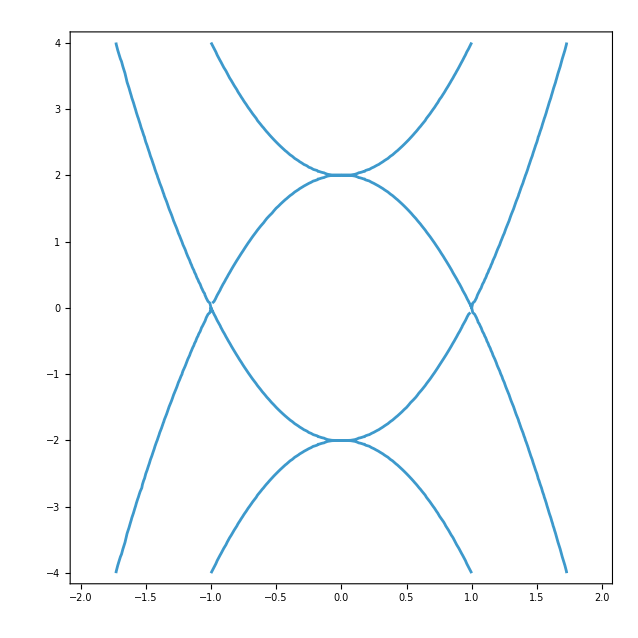

```mathematica
ContourPlot[16 R^8+(-4+U^2)^2-8 R^4 (4+U^2)==0, {R, -2, 2}, {U, -4, 4}]
```

## Generalities

```mathematica
f4[x_]=Array[a[#-1]&, 5].x^Range[0,4]
```

a[0]+x a[1]+x^2 a[2]+x^3 a[3]+x^4 a[4]

```mathematica
f4[a]
```

a[0]+a a[1]+a^2 a[2]+a^3 a[3]+a^4 a[4]

```mathematica
f4'[a]
```

a[1]+2 a a[2]+3 a^2 a[3]+4 a^3 a[4]

```mathematica
Solve[{xp==b/(x-a), yp==b^2 y/(x-a)^2}, {x, y}]//Simplify
```

{{x→a+b/xp,y→yp/xp^2}}

```mathematica
Assuming[a[0]+a a[1]+a^2 a[2]+a^3 a[3]+a^4 a[4]==0, FullSimplify[xp^4(y^2-f4[x])/.{x->a+b/xp, y->yp/xp^2}//Simplify]]
Series[%, {xp, 0, 100}]
```

yp^2-xp^4 a[0]-xp^3 (b+a xp) a[1]-xp^2 (b+a xp)^2 a[2]-xp (b+a xp)^3 a[3]-(b+a xp)^4 a[4]

(yp^2-b^4 a[4])-b^3 (a[3]+4 a a[4]) xp-b^2 (a[2]+3 a a[3]+6 a^2 a[4]) xp^2-b (a[1]+2 a a[2]+3 a^2 a[3]+4 a^3 a[4]) xp^3+(-a[0]-a a[1]-a^2 a[2]-a^3 a[3]-a^4 a[4]) xp^4+O[xp]^101

```mathematica
ser1 = Series[(c x +d)^4 f4[(a x + b)/(c x + d)], {x, 0, 100}]//FullSimplify
```

(d^4 a[0]+b d^3 a[1]+b^2 d^2 a[2]+b^3 d a[3]+b^4 a[4])+(c (4 d^3 a[0]+3 b d^2 a[1]+2 b^2 d a[2]+b^3 a[3])+a (d^3 a[1]+2 b d^2 a[2]+3 b^2 d a[3]+4 b^3 a[4])) x+(c^2 (6 d^2 a[0]+3 b d a[1]+b^2 a[2])+a c (3 d^2 a[1]+4 b d a[2]+3 b^2 a[3])+a^2 (d^2 a[2]+3 b d a[3]+6 b^2 a[4])) x^2+(c^3 (4 d a[0]+b a[1])+a c^2 (3 d a[1]+2 b a[2])+a^2 c (2 d a[2]+3 b a[3])+a^3 (d a[3]+4 b a[4])) x^3+(c^4 a[0]+a c^3 a[1]+a^2 c^2 a[2]+a^3 c a[3]+a^4 a[4]) x^4+O[x]^101

```mathematica
Coefficient[ser1, x^4]/f4[a/c]//Simplify
```

c^4

```mathematica
Coefficient[ser1, x^3]//Expand
Collect[%, Array[a[#-1]&, 5]]
```

4 c^3 d a[0]+b c^3 a[1]+3 a c^2 d a[1]+2 a b c^2 a[2]+2 a^2 c d a[2]+3 a^2 b c a[3]+a^3 d a[3]+4 a^3 b a[4]

4 c^3 d a[0]+(b c^3+3 a c^2 d) a[1]+(2 a b c^2+2 a^2 c d) a[2]+(3 a^2 b c+a^3 d) a[3]+4 a^3 b a[4]

```mathematica
f4'[a/c]//Expand
```

a[1]+(2 a a[2])/c+(3 a^2 a[3])/c^2+(4 a^3 a[4])/c^3

a^3 a[1]+2 a^2 c a[2]+3 a c^2 a[3]+4 c^3 a[4]

```mathematica
rhs = (1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X))
```

(1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X))

## Method 1

```mathematica
(x+c)^4(Y^2-rhs)/.{X->a+b/(x+c),Y->y/(x+c)^2}//Expand//Simplify;
ser1 = Series[%, {x, 0, 100}]
```

(-b^4-2 b^3 c (2 a+U)-b^2 c^2 (2+6 a^2-4 R^4+6 a U+U^2)-2 b c^3 (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-c^4 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))+y^2)+(-2 b^3 (2 a+U)-2 b^2 c (2+6 a^2-4 R^4+6 a U+U^2)-6 b c^2 (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-4 c^3 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x+(-b^2 (2+6 a^2-4 R^4+6 a U+U^2)-6 b c (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-6 c^2 (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x^2+(-2 b (2 a^3+U+3 a^2 U+a (2-4 R^4+U^2))-4 c (1+a^4+2 a U+2 a^3 U+a^2 (2-4 R^4+U^2))) x^3+(-1-2 a^2-a^4+4 a^2 R^4-2 a U-2 a^3 U-a^2 U^2) x^4+O[x]^101

```mathematica
sol1 = Solve[Coefficient[ser1, x^4]==0, a]
```

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2))}}

```mathematica
Coefficient[ser1, x^3]/.sol1//FullSimplify
First@Solve[#==-4, b]&/@%//FullSimplify;
sol2 = MapThread[Join, {sol1, %}]
```

{-2 b R^2 (-4-(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))),-2 b R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2))),2 b R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))),2 b R^2 (-4-(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))}

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2)),b→-2/(R^2 (4+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2)),b→2/(R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2)),b→-2/(R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2)),b→2/(R^2 (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2))))}}

```mathematica
Coefficient[ser1, x^2]/.sol2//FullSimplify
First@Solve[#==0, c]&/@%//FullSimplify;
sol3 = MapThread[Join, {sol2, %}]
```

{(4 (4-96 c R^12-U^2+6 R^2 (U+√(-4+(-2 R^2+U)^2))+48 c R^10 (4 U+√(-4+(-2 R^2+U)^2))-72 c R^8 (-2+U (2 U+√(-4+(-2 R^2+U)^2)))+12 c R^6 (-4 √(-4+(-2 R^2+U)^2)+U (-12+4 U^2+3 U √(-4+(-2 R^2+U)^2)))-2 R^4 (4+3 c (-4+U^2) (-2+U (U+√(-4+(-2 R^2+U)^2))))))/(R^4 (4+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2)))^2),1/(2 R^4 (-4+(-2 R^2+U)^2))((16-96 c) R^8-8 R^6 ((2-12 c) U+√(-4+(-2 R^2+U)^2))+4 R^4 (-4-6 c (-4+U^2)+U √(-4+(-2 R^2+U)^2))-(-2+U) (2+U) (-2+U (U+√(-4+(-2 R^2+U)^2)))+2 R^2 (2 √(-4+(-2 R^2+U)^2)+U (-2+U (2 U+√(-4+(-2 R^2+U)^2))))),-((4 (-4+96 c R^12+U^2+6 R^2 (U+√(-4+(2 R^2+U)^2))+48 c R^10 (4 U+√(-4+(2 R^2+U)^2))+72 c R^8 (-2+U (2 U+√(-4+(2 R^2+U)^2)))+12 c R^6 (-4 √(-4+(2 R^2+U)^2)+U (-12+4 U^2+3 U √(-4+(2 R^2+U)^2)))+R^4 (8+6 c (-4+U^2) (-2+U (U+√(-4+(2 R^2+U)^2))))))/(R^4 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^2)),1/(2 R^4 (-4+(2 R^2+U)^2))((16-96 c) R^8+8 R^6 ((2-12 c) U+√(-4+(2 R^2+U)^2))+4 R^4 (-4-6 c (-4+U^2)+U √(-4+(2 R^2+U)^2))-(-2+U) (2+U) (-2+U (U+√(-4+(2 R^2+U)^2)))-2 R^2 (2 √(-4+(2 R^2+U)^2)+U (-2+U (2 U+√(-4+(2 R^2+U)^2)))))}

{{a→1/2 (2 R^2-U-√(-4+(-2 R^2+U)^2)),b→-2/(R^2 (4+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2)))),c→-(4-8 R^4-U^2+6 R^2 (U+√(-4+(-2 R^2+U)^2)))/(6 R^4 (-4+(-2 R^2+U)^2) (2+(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))},{a→1/2 (2 R^2-U+√(-4+(-2 R^2+U)^2)),b→2/(R^2 (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))),c→1/(24 R^4 (-4+(-2 R^2+U)^2))(16 R^8-8 R^6 (2 U+√(-4+(-2 R^2+U)^2))+4 R^4 (-4+U √(-4+(-2 R^2+U)^2))-(-4+U^2) (-2+U (U+√(-4+(-2 R^2+U)^2)))+2 R^2 (2 √(-4+(-2 R^2+U)^2)+U (-2+U (2 U+√(-4+(-2 R^2+U)^2)))))},{a→1/2 (-2 R^2-U-√(-4+(2 R^2+U)^2)),b→-2/(R^2 (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))),c→-(-4+8 R^4+U^2+6 R^2 (U+√(-4+(2 R^2+U)^2)))/(6 R^4 (-4+(2 R^2+U)^2) (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))},{a→1/2 (-2 R^2-U+√(-4+(2 R^2+U)^2)),b→2/(R^2 (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))),c→1/(24 R^4 (-4+(2 R^2+U)^2))(16 R^8+8 R^6 (2 U+√(-4+(2 R^2+U)^2))+4 R^4 (-4+U √(-4+(2 R^2+U)^2))-(-2+U) (2+U) (-2+U (U+√(-4+(2 R^2+U)^2)))-2 R^2 (2 √(-4+(2 R^2+U)^2)+U (-2+U (2 U+√(-4+(2 R^2+U)^2)))))}}

```mathematica
Coefficient[ser1, x]/.sol3//FullSimplify
g2 = First[%];
```

{(8 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)) (-4-(2 R^2-U) (-32 R^10+5 √(-4+(-2 R^2+U)^2)+16 R^8 (5 U+√(-4+(-2 R^2+U)^2))-8 R^6 (-7+10 U^2+4 U √(-4+(-2 R^2+U)^2))+4 R^4 (-5 √(-4+(-2 R^2+U)^2)+U (-21+10 U^2+6 U √(-4+(-2 R^2+U)^2)))-2 R^2 (13+U (-10 √(-4+(-2 R^2+U)^2)+U (-21+5 U^2+4 U √(-4+(-2 R^2+U)^2))))+U (13+U (-5 √(-4+(-2 R^2+U)^2)+U (-7+U (U+√(-4+(-2 R^2+U)^2))))))))/(3 R^8 (-4+(-2 R^2+U)^2) (8+6 (2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))+(-2 R^2+U)^2 (-2 R^2+U+√(-4+(-2 R^2+U)^2))^2)^3),-((16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)) (-4-(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))/(3 R^8 (-4+(-2 R^2+U)^2) (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))^3),(8 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)) (-4+(2 R^2+U) (32 R^10+5 √(-4+(2 R^2+U)^2)+16 R^8 (5 U+√(-4+(2 R^2+U)^2))+8 R^6 (-7+10 U^2+4 U √(-4+(2 R^2+U)^2))+4 R^4 (-5 √(-4+(2 R^2+U)^2)+U (-21+10 U^2+6 U √(-4+(2 R^2+U)^2)))+2 R^2 (13+U (-10 √(-4+(2 R^2+U)^2)+U (-21+5 U^2+4 U √(-4+(2 R^2+U)^2))))+U (13+U (-5 √(-4+(2 R^2+U)^2)+U (-7+U (U+√(-4+(2 R^2+U)^2))))))))/(3 R^8 (-4+(2 R^2+U)^2) (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^3 (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^3),((16 R^8+(-4+U^2)^2-8 R^4 (2+U^2)) (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))/(3 R^8 (-4+(2 R^2+U)^2) (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))^3)}

```mathematica
(Normal[ser1]/.{x->0,y->0})/.sol3//FullSimplify
g3 = First[%]
```

{(16 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)) (-2+(2 R^2-U) (-3+(-2 R^2+U)^2) (8 R^6+√(-4+(-2 R^2+U)^2)-4 R^4 (3 U+√(-4+(-2 R^2+U)^2))+R^2 (-6+6 U^2+4 U √(-4+(-2 R^2+U)^2))-U (-3+U (U+√(-4+(-2 R^2+U)^2))))))/(27 R^12 (-4+(-2 R^2+U)^2) (8+6 (2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))+(-2 R^2+U)^2 (-2 R^2+U+√(-4+(-2 R^2+U)^2))^2)^4),((4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)) (-2-(2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))))/(27 R^12 (-4+(-2 R^2+U)^2) (-4+(2 R^2-U) (2 R^2-U+√(-4+(-2 R^2+U)^2)))^4),(16 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)) (-2+(2 R^2+U) (-3+(2 R^2+U)^2) (8 R^6-√(-4+(2 R^2+U)^2)+4 R^4 (3 U+√(-4+(2 R^2+U)^2))+R^2 (-6+6 U^2+4 U √(-4+(2 R^2+U)^2))+U (-3+U (U+√(-4+(2 R^2+U)^2))))))/(27 R^12 (-4+(2 R^2+U)^2) (-4+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^4 (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2)))^4),((4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)) (-2+(2 R^2+U) (2 R^2+U+√(-4+(2 R^2+U)^2))))/(27 R^12 (-4+(2 R^2+U)^2) (4+(2 R^2+U) (-2 R^2-U+√(-4+(2 R^2+U)^2)))^4)}

(16 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2)) (-2+(2 R^2-U) (-3+(-2 R^2+U)^2) (8 R^6+√(-4+(-2 R^2+U)^2)-4 R^4 (3 U+√(-4+(-2 R^2+U)^2))+R^2 (-6+6 U^2+4 U √(-4+(-2 R^2+U)^2))-U (-3+U (U+√(-4+(-2 R^2+U)^2))))))/(27 R^12 (-4+(-2 R^2+U)^2) (8+6 (2 R^2-U) (-2 R^2+U+√(-4+(-2 R^2+U)^2))+(-2 R^2+U)^2 (-2 R^2+U+√(-4+(-2 R^2+U)^2))^2)^4)

```mathematica
1728g2^3/(g2^3-27g3^2)//Simplify//PowerExpand//FullSimplify
```

((16 R^8+(-4+U^2)^2-8 R^4 (2+U^2))^3)/(R^8 (16 R^8+(-4+U^2)^2-8 R^4 (4+U^2)))

## Method 2

```mathematica
f2 = (c x + d)^4(Y^2-rhs)/.{X->(a x + b)/(c x + d), Y->(a d - b c)/(c x + d)^2 y}/.{d->(1+b c)/a}//Simplify;
ser2 = Series[f2, {x, 0, 100}]
```

(-(((1+b c)^2+a b (a b-2 (1+b c) R^2+U+b c U)) ((1+b c)^2+a b (a b+(1+b c) (2 R^2+U))))/a^4+y^2)+1/a^4(-(((1+b c)^2+a b (a b-2 (1+b c) R^2+U+b c U)) (2 a c (1+b c)+a^2 (2 a b+2 R^2+4 b c R^2+U+2 b c U)))-(2 a c (1+b c)+a^2 (2 a b-2 R^2-4 b c R^2+U+2 b c U)) ((1+b c)^2+a b (a b+(1+b c) (2 R^2+U)))) x+1/a^2(-2 a^2-6 a^4 b^2-12 a^2 b c-6 c^2-12 a^2 b^2 c^2-12 b c^3-6 b^2 c^4+4 a^2 R^4+24 a^2 b c R^4+24 a^2 b^2 c^2 R^4-6 a^3 b U-6 a c U-12 a^3 b^2 c U-18 a b c^2 U-12 a b^2 c^3 U-a^2 U^2-6 a^2 b c U^2-6 a^2 b^2 c^2 U^2) x^2-1/a 2 (2 a^4 b+2 a^2 c+4 a^2 b c^2+2 c^3+2 b c^4-4 a^2 c R^4-8 a^2 b c^2 R^4+a^3 U+4 a^3 b c U+3 a c^2 U+4 a b c^3 U+a^2 c U^2+2 a^2 b c^2 U^2) x^3-(a^2+c^2-2 a c R^2+a c U) (a^2+c^2+2 a c R^2+a c U) x^4+O[x]^101

```mathematica
eqns = {
Coefficient[ser2, x^4]==0,
Coefficient[ser2, x^2]==0,
Coefficient[ser2, x^3]==-4
}//FullSimplify
```

{(a^2+c^2+a c (-2 R^2+U)) (a^2+c^2+a c (2 R^2+U))==0,6 a^3 b^2+(6 c^2 (1+b c)^2)/a+6 a^2 b (1+2 b c) U+6 c (1+b c) (1+2 b c) U+a (1+6 b c (1+b c)) (2-4 R^4+U^2)==0,2 a^3 b+(2 c^3 (1+b c))/a+c^2 (3+4 b c) U+a^2 (U+4 b c U)+a c (1+2 b c) (2-4 R^4+U^2)==2}

```mathematica
sol = Solve[eqns, {a, b, c}]//ExpandAll//FullSimplify;
```

```mathematica
Coefficient[ser2,x]/.sol//FullSimplify;
If[Equal@@%, Print["All equal"], Print["Not equal"]]; g2=First[%]
```

All equal

1/12 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2))

```mathematica
(Normal[ser2]/.{x->0,y->0})/.sol//FullSimplify;
If[Equal@@%, Print["All equal"], Print["Not equal"]]; g3=First[%]
```

All equal

1/216 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2))

## GPT suggestion

```mathematica
f1 = w+1/w+1/R^2(X+1/X+U)
```

1/w+w+(U+1/X+X)/R^2

```mathematica
Y^2-(R^2(X-1/X)(w-1/w))^2/.Solve[f1==0, w]//FullSimplify
%/.Solve[X+1/X==x, X]//FullSimplify//Flatten;
If[Equal@@%, Print["All Equal"], Print["Not equal"]]; rhs2 = First[%]
```

{-((-1+X^2)^2 (1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X)))/X^4+Y^2,-((-1+X^2)^2 (1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X)))/X^4+Y^2}

All Equal

4 R^4 (-4+x^2)-(U+x)^2 (-4+x^2)+Y^2

```mathematica
Factor[Simplify[-rhs2/.{Y->0}]]
```

(-2+x) (2+x) (-2 R^2+U+x) (2 R^2+U+x)

```mathematica
m2 = {x->2+1/x1, Y->y1/x1^2};
rhs3 = x1^4 rhs2/.m2//Simplify
```

4 R^4 x1^2 (1+4 x1)-(1+4 x1) (1+(2+U) x1)^2+y1^2

```mathematica
Series[rhs3, {x1, 0, 100}]
```

(-1+y1^2)+(-8-2 U) x1+(-20+4 R^4-12 U-U^2) x1^2+(16 R^4-4 (2+U)^2) x1^3+O[x1]^101

## Node param

```mathematica
Solve[First[rhs0]==0, X]
```

{{X→-1},{X→-1},{X→-1+2 R^2-2 √(-R^2+R^4)},{X→-1+2 R^2+2 √(-R^2+R^4)}}

```mathematica
Solve[2(1-2R^2-t)/(t^2-1)==-1, t]
```

{{t→1-2 R},{t→1+2 R}}

```mathematica
m2 = Solve[z==(t-1+2R)/(t-1-2R), t]//Simplify
```

{{t→(-1+z+2 R (1+z))/(-1+z)}}

```mathematica
{-(2 (-1+2 R^2+t))/(-1+t^2),((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))}
%/.First@m2//Simplify//Factor
```

{-(2 (-1+2 R^2+t))/(-1+t^2),((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))}

{-((-1+z) (1-R+z+R z))/((1+z) (-1+R+z+R z)),((1+z) (1-R+z+R z))/((-1+z) (-1+R+z+R z))}

```mathematica
{-((-1+z) (1-R+z+R z))/((1+z) (-1+R+z+R z)),((1+z) (1-R+z+R z))/((-1+z) (-1+R+z+R z))}/.{z->0}//Simplify
```

{-1,1}

```mathematica
Limit[{-((-1+z) (1-R+z+R z))/((1+z) (-1+R+z+R z)),((1+z) (1-R+z+R z))/((-1+z) (-1+R+z+R z))}, z->Infinity]//Simplify
```

{-1,1}

```mathematica
f1/.First[disc0sol]/.Thread[{X, w}->{-((-1+z) (1-R+z+R z))/((1+z) (-1+R+z+R z)),((1+z) (1-R+z+R z))/((-1+z) (-1+R+z+R z))}]//FullSimplify
```

0

```mathematica
BlochWignerLi2[z_]:=Im[PolyLog[2,z]+Arg[1-z]Log[Abs[z]]];dvec={1,1,-1,-1};evec={1,1,-1,-1};
avec={1, (1-R)/(1+R), -1, (R-1)/(R+1)};bvec={-1,(1-R)/(1+R), 1, (R-1)/(R+1)};
A=Sum[dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]],{j,Length[dvec]},{k,Length[evec]}]
```

2 BW[-1]-BW[(1-R)/(-1+R)]-BW[(-1+R)/(1-R)]+BW[-(1-R)/(1+R)]-BW[(1-R)/(1+R)]-BW[-(-1+R)/(1+R)]+BW[(-1+R)/(1+R)]-BW[-(1+R)/(1-R)]+BW[(1+R)/(1-R)]+BW[-(1+R)/(-1+R)]-BW[(1+R)/(-1+R)]

```mathematica
Simplify[A]
```

-2 (BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])

```mathematica
rules={BW[(1+R)/(1-R)]->-BW[(1-R)/(1+R)], BW[(1+R)/(-1+R)]->-BW[(R-1)/(R+1)]}
```

{BW[(1+R)/(1-R)]→-BW[(1-R)/(1+R)],BW[(1+R)/(-1+R)]→-BW[(-1+R)/(1+R)]}

```mathematica
Simplify[A]/.rules//Simplify
```

-4 BW[(1-R)/(1+R)]+4 BW[(-1+R)/(1+R)]

```mathematica
D[PolyLog[2, ], z]
```

-Log[1-z]/z

```mathematica
Exp[Pi I (-1/2)]
```

-ⅈ

```mathematica
Exp[Pi I m/2]/.{m->m-1}
```

ⅇ^(1/2 ⅈ (-1+m) π)

```mathematica
61.3*35
```

2145.5

```mathematica
BlochWignerLi2[z]
```

Im[PolyLog[2,z]]+Arg[1-z] Log[Abs[z]]

```mathematica
ComplexPlot3D[PolyLog[2,z], {z, -2-2I, 2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[BlochWignerLi2[z], {z, -1-1I, 1+I}]
```

-Graphics3D-

```mathematica
BlochWignerLi2[.3+.5I]
```

0.902657

```mathematica
Arg[4]
```

0

## Five Term

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[1-z]Log[z]}};
```

```mathematica
Li2FiveTerm[x_,y_]:=Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y] - (Pi^2/6-Log[x]Log[1-x]-Log[y]Log[1-y]+Log[(1-x)/(1-x y)]Log[(1-y)/(1-x y)]);
```

```mathematica
(* This does NOT work. See Li2FiveTerm checkli25termcheck *)
NNFiveTerm[x_,y_]:=Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y]-1/2 (π^2-Log[1-x] Log[x]-Log[1-y] Log[y]-Log[x y] Log[1-x y]-Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]);
```

```mathematica
Li2Eval = {Li2[z_]:>PolyLog[2,z]};
```

```mathematica
ClearAll[getLinearFactorsData];
getLinearFactorsData[expr_,var_]:=Module[{t,num,den,fn,fd,all,linear},(*make sure it's really a single rational expression*)
t=Together[expr];
num=Numerator[t];
den=Denominator[t];
(*factor numerator and denominator in var*)
fn=Rest@FactorList[num];
(*{{factor,exp},...}*)
fd=Rest@FactorList[den];
(*denominator factors get negative exponents*)all=Join[fn,{{#[[1]],-#[[2]]}&/@fd}//Flatten[#,1]&];
(*keep only true linear polynomials in var*)linear=Select[all,PolynomialQ[First[#],var]&&Exponent[First[#],var]==1&];
(*extract exponents and roots*)
{
(*(a) exponents*)
linear[[All,2]],
(*(b) roots:for a z+b==0->z=-b/a*)Simplify[-Coefficient[#[[1]],var,0]/Coefficient[#[[1]],var,1]]&/@linear
}];

(* test *)
expr=-(((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)));
{exponents,roots}=getLinearFactorsData[expr,z];
exponents
roots
ClearAll[expr,exponents,roots]
```

{1,1,-1,-1}

{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}

```mathematica
sol[1] = {-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))};
sol[2] = {((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),-((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))};
sol[3] = {((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))};
sol[4] = {-((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),-((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))};
```

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
Print[sol[n]];
vX = Echo@getLinearFactorsData[First[sol[n]], z];
vw = Echo@getLinearFactorsData[Last[sol[n]], z];
dvec=First[vX];
evec=First[vw];
avec=Last[vX];
bvec=Last[vw];

{Xat0, wat0} = Echo[sol[n]/.{z->0}//Simplify];
{Xatinf, watinf} = Echo[Limit[sol[n],z->Infinity]//Simplify];
]
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
```

{-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))}

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

{-1,1}

{-1,1}

1/2 (ⅈ (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+1/π(-2 Li2[(1-R)/(1+R)]+2 Li2[(-1+R)/(1+R)]+2 Li2[(1+R)/(1-R)]-2 Li2[(1+R)/(-1+R)]-ⅈ π Log[1/(1-R)]+ⅈ π Log[R/(-1+R)]-ⅈ π Log[1/(1+R)]+Log[1/(1-R)] Log[(1-R)/(1+R)]-Log[R/(-1+R)] Log[(1-R)/(1+R)]+Log[1/(1+R)] Log[(1-R)/(1+R)]+Log[1/(1-R)] Log[(-1+R)/(1+R)]-Log[R/(-1+R)] Log[(-1+R)/(1+R)]+Log[1/(1+R)] Log[(-1+R)/(1+R)]+ⅈ π Log[R/(1+R)]-Log[(1-R)/(1+R)] Log[R/(1+R)]-Log[(-1+R)/(1+R)] Log[R/(1+R)]))

```mathematica
Simplify[R D[B, R]]/.{Li2'[x_]:>-Log[1-x]/x}//Simplify
Simplify[R D[%, R]]//Simplify
```

-(-ⅈ π+Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])/π

(4 R)/(π-π R^2)

```mathematica
Cases[B, Li2[__], Infinity]
```

{Li2[(1-R)/(1+R)],Li2[(-1+R)/(1+R)],Li2[(1+R)/(1-R)],Li2[(1+R)/(-1+R)]}

```mathematica
Li2[(1+R)/(1-R)]/.Li2Rules/.Li2Rules/.Li2Rules//Simplify;
Select[Flatten[%], !FreeQ[#, Li2[(1-R)/(1+R)]]&]
```

{1/6 (-π^2-6 Li2[(1-R)/(1+R)]-6 Log[(-1+R)/(1+R)]^2+3 Log[(1+R)/(-1+R)]^2),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2)}

```mathematica
Li2[(1+R)/(-1+R)]/.Li2Rules/.Li2Rules/.Li2Rules//Simplify;
Select[Flatten[%], !FreeQ[#, Li2[(R-1)/(1+R)]]&]
```

{1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-6 Log[(1-R)/(1+R)]^2+3 Log[(1+R)/(1-R)]^2),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2),1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2)}

```mathematica
(* checked *)
rules={
Li2[(1+R)/(1-R)]->1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),
Li2[(1+R)/(-1+R)]->1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2)

};
```

```mathematica
b1 = B/.rules//Simplify
```

-1/(2 π)(π^2+4 Li2[(1-R)/(1+R)]-4 Li2[(-1+R)/(1+R)]+ⅈ π Log[1/(1-R)]-ⅈ π Log[R/(-1+R)]+ⅈ π Log[1/(1+R)]+ⅈ π Log[(1-R)/(1+R)]-Log[1/(1-R)] Log[(1-R)/(1+R)]+Log[R/(-1+R)] Log[(1-R)/(1+R)]-Log[1/(1+R)] Log[(1-R)/(1+R)]-Log[(1-R)/(1+R)]^2-ⅈ π Log[(-1+R)/(1+R)]-Log[1/(1-R)] Log[(-1+R)/(1+R)]+Log[R/(-1+R)] Log[(-1+R)/(1+R)]-Log[1/(1+R)] Log[(-1+R)/(1+R)]+Log[(-1+R)/(1+R)]^2-ⅈ π Log[R/(1+R)]+Log[(1-R)/(1+R)] Log[R/(1+R)]+Log[(-1+R)/(1+R)] Log[R/(1+R)])

```mathematica
NNFiveTerm[R, -1]
%/.{R->RandomComplex[]}/.Li2Eval
```

Li2[-1]+Li2[R]+Li2[2/(1+R)]+Li2[(1-R)/(1+R)]+Li2[1+R]+1/2 (-π^2+ⅈ π Log[2]+Log[-2/(-1-R)] Log[-(-1+R)/(-1-R)]+Log[1-R] Log[R]+Log[(-1+R)/(-1-R)] Log[-(2 R)/(-1-R)]+Log[-R] Log[1+R])

-0.675266+2.01173 ⅈ

```mathematica
Li2[2/(1+R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1+R)/2]-3 Log[1/2 (-1-R)]^2),1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)])}

```mathematica
Li2[-1]/.Li2Rules//Simplify
```

{-π^2/6-Li2[-1],1/6 (π^2-6 Li2[2]-6 ⅈ π Log[2])}

```mathematica
rules={
Li2[2/(1+R)]->1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]),
Li2[-1]->-π^2/12
};
```

```mathematica
NNFiveTerm[R, -1]/.rules//Simplify
Solve[%==0, Li2[(1-R)/(1+R)]];
B2=B1/.First[%]/.{Li2[-1]->-π^2/12}//Simplify
```

Li2[R]+1/12 (-5 π^2+12 Li2[(1-R)/(1+R)]-12 Li2[(-1+R)/(1+R)]+12 Li2[1+R]+6 ⅈ π Log[2]+6 Log[1-R] Log[R]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]+6 Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+6 Log[-R] Log[1+R])

-1/(6 π)(-2 π^2+12 Li2[R]+12 Li2[1+R]+6 ⅈ π Log[2]-3 ⅈ π Log[1/(1-R)]+6 Log[1-R] Log[R]+3 ⅈ π Log[R/(-1+R)]-3 ⅈ π Log[1/(1+R)]+3 ⅈ π Log[(1-R)/(1+R)]+Log[64] Log[(1-R)/(1+R)]+3 Log[1/(1-R)] Log[(1-R)/(1+R)]-3 Log[R/(-1+R)] Log[(1-R)/(1+R)]+3 Log[1/(1+R)] Log[(1-R)/(1+R)]+3 Log[(1-R)/(1+R)]^2-3 ⅈ π Log[(-1+R)/(1+R)]-Log[64] Log[(-1+R)/(1+R)]+3 Log[1/(1-R)] Log[(-1+R)/(1+R)]-3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]-3 Log[1/(1+R)] Log[(-1+R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2+3 ⅈ π Log[R/(1+R)]+3 Log[(1-R)/(1+R)] Log[R/(1+R)]-3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R])

```mathematica
Li2[1+R]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[1/(1+R)]-3 Log[-1/(1+R)]^2),1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])}

```mathematica
rules={
Li2[1+R]->1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])
};
```

```mathematica
B3 = B2/.rules//Simplify
```

1/(6 π)(12 Li2[-R]-12 Li2[R]-6 ⅈ π Log[2]+3 ⅈ π Log[1/(1-R)]-6 Log[1-R] Log[R]-3 ⅈ π Log[R/(-1+R)]+3 ⅈ π Log[1/(1+R)]-3 ⅈ π Log[(1-R)/(1+R)]-Log[64] Log[(1-R)/(1+R)]-3 Log[1/(1-R)] Log[(1-R)/(1+R)]+3 Log[R/(-1+R)] Log[(1-R)/(1+R)]-3 Log[1/(1+R)] Log[(1-R)/(1+R)]-3 Log[(1-R)/(1+R)]^2+3 ⅈ π Log[(-1+R)/(1+R)]+Log[64] Log[(-1+R)/(1+R)]-3 Log[1/(1-R)] Log[(-1+R)/(1+R)]+3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2-3 ⅈ π Log[R/(1+R)]-3 Log[(1-R)/(1+R)] Log[R/(1+R)]+3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R])

```mathematica
1/(6 π)(-6 ⅈ π Log[2]+3 ⅈ π Log[1/(1-R)]-6 Log[1-R] Log[R]-3 ⅈ π Log[R/(-1+R)]+3 ⅈ π Log[1/(1+R)]-3 ⅈ π Log[(1-R)/(1+R)]-Log[64] Log[(1-R)/(1+R)]-3 Log[1/(1-R)] Log[(1-R)/(1+R)]+3 Log[R/(-1+R)] Log[(1-R)/(1+R)]-3 Log[1/(1+R)] Log[(1-R)/(1+R)]-3 Log[(1-R)/(1+R)]^2+3 ⅈ π Log[(-1+R)/(1+R)]+Log[64] Log[(-1+R)/(1+R)]-3 Log[1/(1-R)] Log[(-1+R)/(1+R)]+3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2-3 ⅈ π Log[R/(1+R)]-3 Log[(1-R)/(1+R)] Log[R/(1+R)]+3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R])
Assuming[0<R<1, FullSimplify[D[%, R]]]
```

1/(6 π)(-6 ⅈ π Log[2]+3 ⅈ π Log[1/(1-R)]-6 Log[1-R] Log[R]-3 ⅈ π Log[R/(-1+R)]+3 ⅈ π Log[1/(1+R)]-3 ⅈ π Log[(1-R)/(1+R)]-Log[64] Log[(1-R)/(1+R)]-3 Log[1/(1-R)] Log[(1-R)/(1+R)]+3 Log[R/(-1+R)] Log[(1-R)/(1+R)]-3 Log[1/(1+R)] Log[(1-R)/(1+R)]-3 Log[(1-R)/(1+R)]^2+3 ⅈ π Log[(-1+R)/(1+R)]+Log[64] Log[(-1+R)/(1+R)]-3 Log[1/(1-R)] Log[(-1+R)/(1+R)]+3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2-3 ⅈ π Log[R/(1+R)]-3 Log[(1-R)/(1+R)] Log[R/(1+R)]+3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R])

(4 ⅈ)/(-1+R^2)

```mathematica
temp = (1/(6 π)(-6 ⅈ π Log[2]+3 ⅈ π Log[1/(1-R)]-6 Log[1-R] Log[R]-3 ⅈ π Log[R/(-1+R)]+3 ⅈ π Log[1/(1+R)]-3 ⅈ π Log[(1-R)/(1+R)]-Log[64] Log[(1-R)/(1+R)]-3 Log[1/(1-R)] Log[(1-R)/(1+R)]+3 Log[R/(-1+R)] Log[(1-R)/(1+R)]-3 Log[1/(1+R)] Log[(1-R)/(1+R)]-3 Log[(1-R)/(1+R)]^2+3 ⅈ π Log[(-1+R)/(1+R)]+Log[64] Log[(-1+R)/(1+R)]-3 Log[1/(1-R)] Log[(-1+R)/(1+R)]+3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2-3 ⅈ π Log[R/(1+R)]-3 Log[(1-R)/(1+R)] Log[R/(1+R)]+3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R]))/.{R->R1+I R2};
```

```mathematica
Plot3D[Im[temp], {R1,-2,2},{R2,-2,2}]
```

-Graphics3D-

```mathematica
Integrate[1/(-1+R^2),R]
```

1/2 Log[1-R]-1/2 Log[1+R]

```mathematica
C2 = (4 Li2[(1-R)/(1+R)]-4 Li2[(-1+R)/(1+R)]+ⅈ π Log[1/(1-R)]-ⅈ π Log[R/(-1+R)]+ⅈ π Log[1/(1+R)]-Log[1/(1-R)] Log[(1-R)/(1+R)]+Log[R/(-1+R)] Log[(1-R)/(1+R)]-Log[1/(1+R)] Log[(1-R)/(1+R)]-Log[(1-R)/(1+R)]^2-Log[1/(1-R)] Log[(-1+R)/(1+R)]+Log[R/(-1+R)] Log[(-1+R)/(1+R)]-Log[1/(1+R)] Log[(-1+R)/(1+R)]+Log[(-1+R)/(1+R)]^2-ⅈ π Log[R/(1+R)]+Log[(1-R)/(1+R)] Log[R/(1+R)]+Log[(-1+R)/(1+R)] Log[R/(1+R)])-2Pi(1/(6 π)(12 Li2[-R]-12 Li2[R]-6 ⅈ π Log[2]+3 ⅈ π Log[1/(1-R)]-6 Log[1-R] Log[R]-3 ⅈ π Log[R/(-1+R)]+3 ⅈ π Log[1/(1+R)]-3 ⅈ π Log[(1-R)/(1+R)]-Log[64] Log[(1-R)/(1+R)]-3 Log[1/(1-R)] Log[(1-R)/(1+R)]+3 Log[R/(-1+R)] Log[(1-R)/(1+R)]-3 Log[1/(1+R)] Log[(1-R)/(1+R)]-3 Log[(1-R)/(1+R)]^2+3 ⅈ π Log[(-1+R)/(1+R)]+Log[64] Log[(-1+R)/(1+R)]-3 Log[1/(1-R)] Log[(-1+R)/(1+R)]+3 Log[R/(-1+R)] Log[(-1+R)/(1+R)]+3 Log[1/(1+R)] Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2-3 ⅈ π Log[R/(1+R)]-3 Log[(1-R)/(1+R)] Log[R/(1+R)]+3 Log[(-1+R)/(1+R)] Log[R/(1+R)]+6 Log[-R] Log[1+R]));
C2 = C2/.{R->R1+I R2}/.{Li2[z_]:>PolyLog[2,z]};
```

```mathematica
Im[C2]/.{R1->.2,R2->.4}
```

2.95312

```mathematica
Plot3D[Im[C2], {R1,-2,2},{R2,-2,2}]
```

-Graphics3D-

#### Li2Rules check

```mathematica
(Li2[z]/.Li2Rules)-Li2[z]/.{Li2[z_]:>PolyLog[2,z]}
ReIm/@%/.{z->z1+I z2}//Flatten
Plot3D[%[[4]], {z1,-2,2}, {z2,-2,2},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

{-π^2/6-1/2 Log[-1/z]^2-PolyLog[2,1/z]-PolyLog[2,z],π^2/6-Log[1-z] Log[z]-PolyLog[2,1-z]-PolyLog[2,z]}

{-π^2/6+Re[-1/2 Log[-1/(z1+ⅈ z2)]^2-PolyLog[2,1/(z1+ⅈ z2)]-PolyLog[2,z1+ⅈ z2]],Im[-1/2 Log[-1/(z1+ⅈ z2)]^2-PolyLog[2,1/(z1+ⅈ z2)]-PolyLog[2,z1+ⅈ z2]],π^2/6+Re[-Log[1-z1-ⅈ z2] Log[z1+ⅈ z2]-PolyLog[2,1-z1-ⅈ z2]-PolyLog[2,z1+ⅈ z2]],Im[-Log[1-z1-ⅈ z2] Log[z1+ⅈ z2]-PolyLog[2,1-z1-ⅈ z2]-PolyLog[2,z1+ⅈ z2]]}

-Graphics3D-

#### Li2FiveTerm check

```mathematica
Li2FiveTerm[x,y]/.{Li2[x_]:>PolyLog[2,x]}/.{x->RandomComplex[],y->RandomComplex[]}
```

2.96077-0.940207 ⅈ

Does NOT WORK

```mathematica
NewFiveTerm[x_,y_] := L[x]+L[y]-L[x y]-L[x(1-y)/(1-x y)]-L[y(1-x)/(1-x y)];
```

```mathematica
t1 := NewFiveTerm[x,y]/.{L[x_]:>Pi/6(PolyLog[2,x]+1/2Log[x]Log[1-x])}/.{x->RandomComplex[],y->RandomComplex[]}
```

```mathematica
AllTrue[Abs/@Table[t1, {i, 10000}], #<10^-10&]
```

True

```mathematica
NewFiveTerm[x,y]/.{L[x_]:>Pi/6(PolyLog[2,x]+1/2Log[x]Log[1-x])}/.{x->RandomComplex[],y->1.2}
```

0.-0.299907 ⅈ

```mathematica
F = 6/Pi NewFiveTerm[x, y]/.{L[x_]:>Pi/6(Li2[x]+1/2Log[x]Log[1-x])}//Simplify
```

1/2 (2 Li2[x]+2 Li2[y]-2 Li2[x y]-2 Li2[(x (-1+y))/(-1+x y)]-2 Li2[((-1+x) y)/(-1+x y)]+Log[1-x] Log[x]+Log[1-y] Log[y]-Log[x y] Log[1-x y]-Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])

```mathematica
Li2FiveTerm[x,y]
```

-π^2/6+Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y]+Log[1-x] Log[x]+Log[1-y] Log[y]-Log[(1-x)/(1-x y)] Log[(1-y)/(1-x y)]

```mathematica
Li2[(x (-1+y))/(-1+x y)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1-x y)/(x-x y)]-3 Log[(1-x y)/(x (-1+y))]^2),1/6 (π^2-6 Li2[(-1+x)/(-1+x y)]-6 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)])}

```mathematica
Li2[((-1+x) y)/(-1+x y)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1-x y)/(y-x y)]-3 Log[(1-x y)/((-1+x) y)]^2),1/6 (π^2-6 Li2[(-1+y)/(-1+x y)]-6 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])}

```mathematica
Li2[x y]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[1/(x y)]-3 Log[-1/(x y)]^2),1/6 (π^2-6 Li2[1-x y]-6 Log[x y] Log[1-x y])}

```mathematica
rules = {Li2[(x (-1+y))/(-1+x y)]->1/6 (π^2-6 Li2[(-1+x)/(-1+x y)]-6 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]), Li2[((-1+x) y)/(-1+x y)]->1/6 (π^2-6 Li2[(-1+y)/(-1+x y)]-6 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]), Li2[x y]->1/6 (π^2-6 Li2[1-x y]-6 Log[x y] Log[1-x y])};
```

```mathematica
F/.rules//Simplify
Solve[%==0,  Li2[x]]
Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y]/.First[%]//Simplify
```

1/2 (-π^2+2 Li2[x]+2 Li2[y]+2 Li2[1-x y]+2 Li2[(-1+x)/(-1+x y)]+2 Li2[(-1+y)/(-1+x y)]+Log[1-x] Log[x]+Log[1-y] Log[y]+Log[x y] Log[1-x y]+Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])

{{Li2[x]→1/2 (π^2-2 Li2[y]-2 Li2[1-x y]-2 Li2[(-1+x)/(-1+x y)]-2 Li2[(-1+y)/(-1+x y)]-Log[1-x] Log[x]-Log[1-y] Log[y]-Log[x y] Log[1-x y]-Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])}}

1/2 (π^2-Log[1-x] Log[x]-Log[1-y] Log[y]-Log[x y] Log[1-x y]-Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])

```mathematica
NNFiveTerm[x_,y_]:=Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y]-1/2 (π^2-Log[1-x] Log[x]-Log[1-y] Log[y]-Log[x y] Log[1-x y]-Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]);
```

```mathematica
t1 :=NNFiveTerm[x,y]/.{Li2[z_]:>PolyLog[2,z]}/.{x->RandomComplex[],y->RandomComplex[]}
```

```mathematica
AllTrue[Abs/@Table[t1, {i, 10000}], #<10^-10&]
```

True

```mathematica
NNFiveTerm[x,y]
```

Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[(1-y)/(1-x y)]+Li2[1-x y]+1/2 (-π^2+Log[1-x] Log[x]+Log[1-y] Log[y]+Log[x y] Log[1-x y]+Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])

## Full Result?

```mathematica
ClearAll[BlochWignerLi2];
BlochWignerLi2[z_]:=Im[PolyLog[2,z]]+Arg[1-z]Log[Abs[z]];
```

```mathematica
repabc = {a->1/b^2,d->1,c->1/b}
```

{a→1/b^2,d→1,c→1/b}

```mathematica
p2 = {u->1/3, m->0};
```

```mathematica
X0[m_,u_]:=-((3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4)));
```

```mathematica
t1[m_,u_]:=-2+Sqrt[1+12m u^2];
```

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc;
bvec={d, b, c}/.repabc;

{Xat0, wat0} = Echo[{alp, bet}];
{Xatinf, watinf} = Echo[{alp, bet}];
]
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
tmp = B/.rules//Simplify
tmp = FullSimplify[%, Im[b]>0]
```

{alp,bet}

{alp,bet}

1/(2 π)(Li2[1/b^3]-3 Li2[1/b^2]+2 Li2[1/b]-3 Li2[b]+Li2[b^2]+Log[1-1/b^3] Log[1/b^2]-2 Log[1-1/b^2] Log[1/b^2]-Log[alp] Log[1/b]-Log[1-1/b^2] Log[1/b]+Log[1-b] Log[1/b]+Log[1/b^2] Log[(-1+b)/b]+Log[1/b] Log[(-1+b)/b]-Log[alp] Log[b]-Log[1-1/b^3] Log[b]+Log[1-1/b^2] Log[b]-2 Log[1-b] Log[b]+Log[(-1+b)/b] Log[b]-Log[1/b] Log[1-b^2]+Log[b] Log[1-b^2]-Log[1/b^2] Log[bet]+Log[1/b] Log[bet]-Log[b] Log[bet])

-1/(4 π)(10 Li2[b]-8 Li2[b^2]+2 Li2[b^3]-2 Log[1-1/b^3] Log[1/b^2]+4 Log[1-1/b^2] Log[1/b^2]+2 Log[alp] Log[1/b]+2 Log[1-1/b^2] Log[1/b]-2 Log[1-b] Log[1/b]-2 Log[1/b^2] Log[(-1+b)/b]-2 Log[1/b] Log[(-1+b)/b]+2 Log[-b]^2+2 Log[alp] Log[b]+2 Log[1-1/b^3] Log[b]-2 Log[1-1/b^2] Log[b]+4 Log[1-b] Log[b]-2 Log[(-1+b)/b] Log[b]-3 Log[-b^2]^2+Log[-b^3]^2+2 Log[1/b] Log[1-b^2]-2 Log[b] Log[1-b^2]+2 Log[1/b^2] Log[bet]-2 Log[1/b] Log[bet]+2 Log[b] Log[bet])

-1/(4 π)(π^2+10 Li2[b]-8 Li2[b^2]+2 Li2[b^3]-2 Log[1/b^2] Log[(-1+b)/b]+4 Log[1-1/b^2] (Log[1/b^2]-Log[b])+2 Log[1-1/b^3] (-Log[1/b^2]+Log[b])+Log[-b^3]^2+2 Log[b] (3 ⅈ π+Log[-1+b]-5 Log[b]-2 Log[1+b])+2 (Log[1/b^2]+2 Log[b]) Log[bet])

```mathematica
FullSimplify[tmp, 0<b<1]//Expand
```

-(5 Li2[b])/(2 π)+(2 Li2[b^2])/π-Li2[b^3]/(2 π)-3 ⅈ Log[b]+(3 Log[1-b] Log[b])/π-Log[b]^2/(4 π)+(4 Log[b] Log[1+b])/π-(3 Log[b] Log[(-1+b) (-1+b^3)])/(2 π)

```mathematica
Coefficient[tmp, Log[bet]]
```

-(Log[1/b^2]+2 Log[b])/(2 π)

```mathematica
Coefficient[tmp, Log[alp]]
```

0

```mathematica
Coefficient[-1/(4 π)(10 Li2[b]-8 Li2[b^2]+2 Li2[b^3]-2 Log[1-1/b^3] Log[1/b^2]+4 Log[1-1/b^2] Log[1/b^2]+2 Log[alp] Log[1/b]+2 Log[1-1/b^2] Log[1/b]-2 Log[1-b] Log[1/b]-2 Log[1/b^2] Log[(-1+b)/b]-2 Log[1/b] Log[(-1+b)/b]+2 Log[-b]^2+2 Log[alp] Log[b]+2 Log[1-1/b^3] Log[b]-2 Log[1-1/b^2] Log[b]+4 Log[1-b] Log[b]-2 Log[(-1+b)/b] Log[b]-3 Log[-b^2]^2+Log[-b^3]^2+2 Log[1/b] Log[1-b^2]-2 Log[b] Log[1-b^2]+2 Log[1/b^2] Log[bet]-2 Log[1/b] Log[bet]+2 Log[b] Log[bet]), Log[alp]]
```

-(2 Log[1/b]+2 Log[b])/(4 π)

```mathematica
Log[1/b^2]+2 Log[b]/.{b->-2}//N
```

0.+6.28319 ⅈ

```mathematica
Log[1/b^2]+2 Log[b]/.{b->2}//N
```

0.

```mathematica
ComplexPlot3D[2 Log[1/b]+2 Log[b], {b,-2-2I, 2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Log[1/b^2]+2 Log[b], {b,-2, 2+2I}]
```

-Graphics3D-

```mathematica
Li2[1/b^3]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),1/6 (π^2-6 Li2[1-1/b^3]-6 Log[1-1/b^3] Log[1/b^3])}

```mathematica
rules={
Li2[1/b]->1/6 (-π^2-6 Li2[b]-3 Log[-b]^2),
Li2[1/b^2]->1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),
Li2[1/b^3]->1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2)
}
```

{Li2[1/b]→1/6 (-π^2-6 Li2[b]-3 Log[-b]^2),Li2[1/b^2]→1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),Li2[1/b^3]→1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2)}

```mathematica
Li2[1/b^3]-3 Li2[1/b^2]+2 Li2[1/b]-3 Li2[b]+Li2[b^2]
%/.rules//Simplify
```

Li2[1/b^3]-3 Li2[1/b^2]+2 Li2[1/b]-3 Li2[b]+Li2[b^2]

-5 Li2[b]+4 Li2[b^2]-Li2[b^3]-Log[-b]^2+3/2 Log[-b^2]^2-1/2 Log[-b^3]^2

```mathematica
B/.{b->Exp[2Pi I/3], alp->1,bet->1}
```

Infinity::indet: Indeterminate expression (-ⅈ) ∞+ⅈ ∞+Li2[1]+Li2[ⅇ^(-(2 ⅈ π)/3)]+2 Li2[ⅇ^(-(2 ⅈ π)/3)]-3 Li2[ⅇ^((2 ⅈ π)/3)]-3 Li2[ⅇ^((2 ⅈ π)/3)]+2/3 ⅈ π Log[1-ⅇ^(-(2 ⅈ π)/3)]+2/3 ⅈ π Log[1-ⅇ^(«1»)]-2/3 ⅈ π Log[1-ⅇ^((«1»)/3)]+2/3 ⅈ π Log[1-ⅇ^((2 ⅈ π)/3)]+2/3 ⅈ π Log[1-ⅇ^((2 ⅈ π)/3)]-4/3 ⅈ π Log[1-ⅇ^((2 ⅈ π)/3)]-4/3 ⅈ π Log[1-ⅇ^((2 ⅈ π)/3)]-2/3 ⅈ π Log[ⅇ^(-(2 ⅈ π)/3) (-1+ⅇ^((2 ⅈ π)/3))]+2/3 ⅈ π Log[ⅇ^(-(2 ⅈ π)/3) (-1+ⅇ^((2 ⅈ π)/3))]+2/3 ⅈ π Log[ⅇ^(-(2 ⅈ π)/3) (-1+ⅇ^((2 ⅈ π)/3))] encountered.

Indeterminate

```mathematica
FullSimplify[B, Im[b]>0]//Expand
%/.{Li2[1/b^3]->0,Log[1-1/b^3]->0}
%/.{b->Exp[2Pi I/3], alp->1,bet->1}//Simplify
%/.Li2Eval//N
```

Li2[1/b^3]/(2 π)-(3 Li2[1/b^2])/(2 π)+Li2[1/b]/π-(3 Li2[b])/(2 π)+Li2[b^2]/(2 π)+(Log[1-1/b^3] Log[1/b^2])/(2 π)-(Log[1-1/b^2] Log[1/b^2])/π+(Log[1/b^2] Log[(-1+b)/b])/(2 π)+1/2 ⅈ Log[b]-(Log[1-1/b^3] Log[b])/(2 π)+(Log[1-1/b^2] Log[b])/π-(Log[-1+b] Log[b])/(2 π)+(Log[b] Log[1+b])/π-(Log[1/b^2] Log[bet])/(2 π)-(Log[b] Log[bet])/π

-(3 Li2[1/b^2])/(2 π)+Li2[1/b]/π-(3 Li2[b])/(2 π)+Li2[b^2]/(2 π)-(Log[1-1/b^2] Log[1/b^2])/π+(Log[1/b^2] Log[(-1+b)/b])/(2 π)+1/2 ⅈ Log[b]+(Log[1-1/b^2] Log[b])/π-(Log[-1+b] Log[b])/(2 π)+(Log[b] Log[1+b])/π-(Log[1/b^2] Log[bet])/(2 π)-(Log[b] Log[bet])/π

-(5 π)/9+(3 (Li2[-(-1)^(1/3)]-2 Li2[(-1)^(2/3)]))/(2 π)+1/3 ⅈ (Log[1+(-1)^(1/3)]-Log[-1+(-1)^(2/3)])

-0.785398-0.969198 ⅈ

#### m=0

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->0})==0, u]//N
```

{{u→0.},{u→0.333333},{u→-0.166667-0.288675 ⅈ},{u→-0.166667+0.288675 ⅈ}}

```mathematica
repmu ={m->0, u->1/3};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-1/2

```mathematica
tt1 = t1[m,u]/.repmu
```

-1

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→(-1-ⅈ √3)/(-1+ⅈ √3),alp→1,bet→1}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval//N
```

{alp,bet}

{alp,bet}

1/(2 π)3 (-2 Li2[(ⅈ-√3)/(ⅈ+√3)]+Li2[(ⅈ+√3)/(ⅈ-√3)]+Log[-(-ⅈ+√3)/(ⅈ+√3)] (-Log[-ⅈ+√3]+Log[ⅈ+√3]))

-0.785398-0.969198 ⅈ

```mathematica
-Pi/4//N
```

-0.785398

#### m=1

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->1})==0, u]//N
```

{{u→-3.02572},{u→0.263185},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ}}

```mathematica
repmu ={m->1, u->0.2631852692187436};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.437619

```mathematica
tt1 = t1[m,u]/.repmu
```

-0.646782

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→-0.72515+0.688591 ⅈ,alp→1.49022,bet→0.819173}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval
```

{alp,bet}

{alp,bet}

(-0.759544-8.32667×10^-16 ⅈ)+0.31831 Li2[-0.72515-0.688591 ⅈ]-0.477465 Li2[-0.72515+0.688591 ⅈ]-0.31831 Li2[0.0516844+0.998663 ⅈ]+0.159155 Li2[0.0516844-0.998663 ⅈ]-0.159155 Li2[0.0516844+0.998663 ⅈ]+0.159155 Li2[0.650192-0.75977 ⅈ]

-0.523599-1.15732 ⅈ

```mathematica
Pi/6//N
```

0.523599

#### m=2

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->2})==0, u]//N
```

{{u→1.},{u→0.227204},{u→-0.257166-0.144985 ⅈ},{u→-0.257166+0.144985 ⅈ}}

```mathematica
repmu ={m->2, u->0.22720363485798575};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.376843

```mathematica
tt1 = t1[m,u]/.repmu
```

-0.503699

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→-0.798222+0.602364 ⅈ,alp→1.83118,bet→0.738984}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval
```

{alp,bet}

{alp,bet}

(-0.646459-0.132626 ⅈ)-0.477465 Li2[-0.798222+0.602364 ⅈ]+0.31831 Li2[-0.798222-0.602364 ⅈ]-0.159155 Li2[0.274316+0.96164 ⅈ]-0.31831 Li2[0.274316+0.96164 ⅈ]+0.159155 Li2[0.274316-0.96164 ⅈ]+0.159155 Li2[0.360292-0.93284 ⅈ]

-0.523599-1.27104 ⅈ

#### m=3

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->3})==0, u]//N
```

{{u→0.203722},{u→0.540285},{u→-0.23867-0.101662 ⅈ},{u→-0.23867+0.101662 ⅈ}}

```mathematica
repmu ={m->3, u->0.20372168044439534};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.332224

```mathematica
tt1 = t1[m,u]/.repmu
```

-0.420731

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→-0.83688+0.547387 ⅈ,alp→2.11012,bet→0.688408}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval
```

{alp,bet}

{alp,bet}

(-0.579238-0.245467 ⅈ)+0.31831 Li2[-0.83688-0.547387 ⅈ]-0.477465 Li2[-0.83688+0.547387 ⅈ]+0.159155 Li2[0.166145-0.986101 ⅈ]+0.159155 Li2[0.400736-0.916194 ⅈ]-0.477465 Li2[0.400736+0.916194 ⅈ]

-0.523599-1.35514 ⅈ

```mathematica
-Pi/6//N
```

-0.523599

#### m=1/2

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->1/2})==0, u]//N
```

{{u→-0.563874},{u→0.290834},{u→-0.22348-0.268351 ⅈ},{u→-0.22348+0.268351 ⅈ}}

```mathematica
repmu ={m->1/2, u->0.29083423009146575};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.474052

```mathematica
tt1 = t1[m,u]/.repmu
```

-0.772194

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→-0.653384+0.757027 ⅈ,alp→1.27668,bet→0.885034}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval
```

{alp,bet}

{alp,bet}

(-0.858751+0.0623671 ⅈ)+0.31831 Li2[-0.653384-0.757027 ⅈ]-0.477465 Li2[-0.653384+0.757027 ⅈ]+0.159155 Li2[-0.14618-0.989258 ⅈ]-0.159155 Li2[-0.14618+0.989258 ⅈ]-0.31831 Li2[-0.14618+0.989258 ⅈ]+0.159155 Li2[0.844407-0.535703 ⅈ]

-0.523599-1.07909 ⅈ

#### m=-1/2

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->-1/2})==0, u]//N
```

{{u→-0.121558-0.278652 ⅈ},{u→-0.121558+0.278652 ⅈ},{u→0.431903-0.0027896 ⅈ},{u→0.431903+0.0027896 ⅈ}}

```mathematica
repmu ={m->-1/2, u->0.43190322710217677-0.002789601440947276 ⅈ};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.0804983-0.33865 ⅈ

```mathematica
tt1 = t1[m,u]/.repmu
```

-1.9791+0.345879 ⅈ

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→1.08572-2.15613 ⅈ,alp→0.393076+0.13601 ⅈ,bet→1.52909-0.257066 ⅈ}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BlochWignerLi2[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
{A, A-1/2/Pi Log[Abs[m]](Arg[1/b^2]-Arg[b])/.repmu/.repbalpbet, %/.Li2Eval}
```

{alp,bet}

{alp,bet}

(-0.260485-0.806132 ⅈ)+0.159155 Li2[-3.47013-4.6819 ⅈ]-0.477465 Li2[-0.102177+0.137857 ⅈ]+0.159155 Li2[-0.0700404-0.0121203 ⅈ]+0.31831 Li2[0.186303+0.369981 ⅈ]-0.477465 Li2[1.08572-2.15613 ⅈ]

{-0.388798,-0.0233215,-0.543461+0.0233215 ⅈ}

```mathematica
0.543460808722009/Pi//N
1/%
```

0.172989

5.78072

```mathematica
{-0.3887980571701058,-0.023321519590772777,-0.543460808722009+0.02332151959076101 ⅈ}//N
```

{-0.388798,-0.0233215,-0.543461+0.0233215 ⅈ}

#### m=1/4

```mathematica
Solve[(m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->1/4})==0, u]//N
```

{{u→-0.253908},{u→0.309368},{u→-0.195954-0.283865 ⅈ},{u→-0.195954+0.283865 ⅈ}}

```mathematica
repmu ={m->1/4, u->0.3093675646689764};
```

```mathematica
x0 = X0[m,u]/.repmu
```

-0.490953

```mathematica
tt1 = t1[m,u]/.repmu
```

-0.865485

```mathematica
repbalpbet = {b->(tt1-Sqrt[6x0])/(tt1+Sqrt[6x0]), alp->(3+tt1)/6/u/.repmu, bet->-18u^2/tt1/(tt1+3)/.repmu}
```

{b→-0.594529+0.804074 ⅈ,alp→1.14993,bet→0.932531}

```mathematica
ClearAll[avec,bvec,dvec,evec,Xat0,wat0,Xatinf,watinf];
With[{n=1},
dvec={1, 1, -1, -1};
evec={2,-1,-1};
avec={a,b,c,d}/.repabc/.repbalpbet;
bvec={d, b, c}/.repabc/.repbalpbet;

{Xat0, wat0} = Echo[{alp, bet}]/.repbalpbet;
{Xatinf, watinf} = Echo[{alp, bet}]/.repbalpbet;
]
A=1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

B1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[Xatinf])//Simplify;

B2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

B3 = 1/2/Pi Log[Xatinf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = B0 + B1 + B2 + B3//Simplify
%/.Li2Eval
```

{alp,bet}

{alp,bet}

(-0.934117+0.0748488 ⅈ)+0.31831 Li2[-0.594529-0.804074 ⅈ]-0.477465 Li2[-0.594529+0.804074 ⅈ]+0.159155 Li2[-0.293071-0.956091 ⅈ]-0.477465 Li2[-0.293071+0.956091 ⅈ]+0.159155 Li2[0.943007-0.332772 ⅈ]

-0.523599-1.02992 ⅈ

```mathematica
Pi/6//N
```

0.523599

## Partial Results

```mathematica
Series[Log[z], {z,1,3}]
```

(z-1)-1/2 (z-1)^2+1/3 (z-1)^3+O[z-1]^4

```mathematica
PL[w_]:=PolyLog[2,1/w];
```

```mathematica
Series[PolyLog[2,z], {z,0,3}]//Simplify
```

z+z^2/4+z^3/9+O[z]^4

```mathematica
Series[PL[w], {w,0,3}]//Simplify
```

1/6 (-π^2-3 Log[-1/w]^2)-w-w^2/4-w^3/9+O[w]^4

```mathematica
Plot3D[Evaluate[ReIm[Log[(z0+z1+I z2)]]/.{z0->0.}], {z1, -.5,.5}, {z2,-.5,.5},
PlotPoints->100
]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[ReIm[PolyLog[2,1/(z0+z1+I z2)]]/.{z0->0.}], {z1, -.5,.5}, {z2,-.5,.5},
PlotPoints->100
]
```

-Graphics3D-

```mathematica
D[PolyLog[2,z],z]
```

-Log[1-z]/z

```mathematica
D[PolyLog[2,z f[z]],z]
```

-(Log[1-z f[z]] (f[z]+z f'[z]))/(z f[z])

```mathematica
PolyLog[1,z]
```

-Log[1-z]

```mathematica
D[PolyLog[1,z], z]
```

1/(1-z)

```mathematica
z D[PolyLog[1,f[z]], z]
```

(z f'[z])/(1-f[z])

```mathematica
-Log[1-x/y]
```

```mathematica
NewFiveTerm[x_,y_] := L[x]+L[y]-L[x y]-L[x(1-y)/(1-x y)]-L[y(1-x)/(1-x y)];
```

```mathematica
NewFiveTerm[x, y]/.{L[x_]:>Li2[x]+1/2Logi[x]Logi[1-x]}/.{Logi[z_]:>-Li1[1-z]}//Simplify//Expand;
Simplify[y D[%, y]]/.{Li2'[z_]:>Li1[z]/z}/.{ Li1'[z_]:>1/(1-z)}//Simplify;
Simplify[y D[%, y]]/.{Li2'[z_]:>Li1[z]/z}/.{ Li1'[z_]:>1/(1-z)}//Simplify;
FullSimplify[%/.{Li1[z_]:>-Log[1-z]}, {Im[x]>0,Im[y]>0}]
```

1/(2 (-1+y)^2 (-1+x y)^2)y (-2 x (1+y^2) ArcTanh[1-(2 (-1+x))/(-1+x y)]-(-1+x y)^2 Log[y]-Log[(-1+x)/(-1+x y)]+Log[((-1+x) y)/(-1+x y)]+x (2 ArcTanh[(1+(-2+x) y)/(1-x y)]+(-1+y)^2 Log[x y]+y (-x y Log[(-1+x)/(-1+x y)]+(-2+y) Log[(-1+y)/(-1+x y)]+2 Log[(x (-1+y))/(-1+x y)]+(-1+x) y Log[((-1+x) y)/(-1+x y)])))

```mathematica
NewFiveTerm[R,-.01+.01I]/.{L[x_]:>Li2[x]+1/2Log[x]Log[1-x]}/.{Li2[-1]->-Pi^2/12}//Simplify//Expand;
%/.{R->RandomComplex[]}/.Li2Eval
```

-2.65413×10^-16-4.29344×10^-17 ⅈ

```mathematica
Abs[4.215378046623641*^-16+8.396061623727746*^-16 ⅈ]
```

9.39485×10^-16

-π^2/12-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]-Li2[(2 R)/(1+R)]+1/2 ⅈ π Log[2]+1/2 Log[1-R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 Log[-R] Log[1+R]-1/2 Log[(2 R)/(1+R)] Log[1-(2 R)/(1+R)]

-π^2/12+1/2 ⅈ π Log[2]+1/2 Log[1-R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 Log[-R] Log[1+R]-1/2 Log[(2 R)/(1+R)] Log[1-(2 R)/(1+R)]-PolyLog[2,-R]+PolyLog[2,R]-PolyLog[2,(-1+R)/(1+R)]-PolyLog[2,(2 R)/(1+R)]

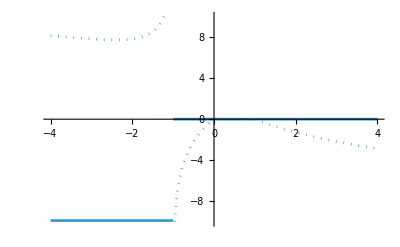

```mathematica
NewFiveTerm[R,-1]/.{L[x_]:>Li2[x]+1/2Log[x]Log[1-x]}/.{Li2[-1]->-Pi^2/12}//Simplify//Expand
%/.Li2Eval
ReImPlot[%, {R, -4, 4},
PlotRange->{{-4, 4},{-10, 10}}
]
```

```mathematica
NewFiveTerm[R,-1]/.{L[x_]:>Li2[x]+1/2Log[x]Log[1-x]}/.{Li2[-1]->-Pi^2/12}//Simplify//Expand
%/.{R->R1+I R2}/.Li2Eval/.{Logi->Log}
Plot3D[Re[%], {R1,-100,100}, {R2,-100,100}]
```

-π^2/12-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]-Li2[(2 R)/(1+R)]+1/2 ⅈ π Log[2]+1/2 Log[1-R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 Log[-R] Log[1+R]-1/2 Log[(2 R)/(1+R)] Log[1-(2 R)/(1+R)]

-π^2/12+1/2 ⅈ π Log[2]+1/2 Log[1-R1-ⅈ R2] Log[R1+ⅈ R2]-1/2 Log[2/(1+R1+ⅈ R2)] Log[(-1+R1+ⅈ R2)/(1+R1+ⅈ R2)]-1/2 Log[1-(2 (R1+ⅈ R2))/(1+R1+ⅈ R2)] Log[(2 (R1+ⅈ R2))/(1+R1+ⅈ R2)]-1/2 Log[-R1-ⅈ R2] Log[1+R1+ⅈ R2]-PolyLog[2,-R1-ⅈ R2]+PolyLog[2,R1+ⅈ R2]-PolyLog[2,(-1+R1+ⅈ R2)/(1+R1+ⅈ R2)]-PolyLog[2,(2 (R1+ⅈ R2))/(1+R1+ⅈ R2)]

-Graphics3D-

```mathematica
Fold
```

```mathematica
Simplify[NestList[{#[[2]],(1-#[[2]])/#[[1]]}&, {x0, x1},5]]
```

{{x0,x1},{x1,(1-x1)/x0},{(1-x1)/x0,(-1+x0+x1)/(x0 x1)},{(-1+x0+x1)/(x0 x1),(1-x0)/x1},{(1-x0)/x1,x0},{x0,x1}}

```mathematica
{x1,(1-x1)/x0}==={x0, x1}
```

False

```mathematica
FixedPoint
```

```mathematica
Log[-3+.01I]
```

1.09862+3.13826 ⅈ

```mathematica
Log[-3-.01I]
```

1.09862-3.13826 ⅈ

```mathematica
Assuming[eps>0, Integrate[-Log[1-t]/t, {t,1-I eps,1+I eps}]]
```

-PolyLog[2,1-ⅈ eps]+PolyLog[2,1+ⅈ eps]

```mathematica
Limit[-PolyLog[2,2-ⅈ eps]+PolyLog[2,2+ⅈ eps], eps->0, Direction->"FromAbove"]
```

Conjugate[PolyLog[2,2]]-PolyLog[2,2]

```mathematica
Series[-PolyLog[2,2-ⅈ eps]+PolyLog[2,2+ⅈ eps], {eps, 0, 0}]//Simplify
```

-2 ⅈ π Ceiling[Arg[-ⅈ eps]/(2 π)] Log[2]+2 ⅈ π Ceiling[Arg[ⅈ eps]/(2 π)] Log[2]+2 ⅈ π Floor[(π+Arg[-ⅈ eps])/(2 π)] Log[2]-2 ⅈ π Floor[(π+Arg[ⅈ eps])/(2 π)] Log[2]+(π eps+O[eps]^2)

```mathematica
PolyLog[2,2+I.01]
```

2.45172+2.17763 ⅈ

```mathematica
PolyLog[2,2-I.01]
```

2.45172-2.17763 ⅈ

```mathematica
Series[1/(x-I eps s), {eps, 0, 4}]
```

1/x+(ⅈ s eps)/x^2-(s^2 eps^2)/x^3-(ⅈ s^3 eps^3)/x^4+(s^4 eps^4)/x^5+O[eps]^5

```mathematica
NewFiveTerm[R, -1]/.{L[x_]:>Li2[x]+1/2Log[x]Log[1-x]}//Simplify//Expand
Simplify[R D[%, R]]/.{Li2'[z_]:>-Log[1-z]/z}//Simplify
Simplify[R D[%, R]]//Simplify
Assuming[Im[R]>0, FullSimplify[%]]
```

Li2[-1]-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]-Li2[(2 R)/(1+R)]+1/2 ⅈ π Log[2]+1/2 Log[1-R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 Log[-R] Log[1+R]-1/2 Log[(2 R)/(1+R)] Log[1-(2 R)/(1+R)]

-1/(2 (-1+R^2))((-1+R^2) Log[1-R]+(-1+R) R Log[-R]-R Log[R]-R^2 Log[R]-2 R Log[1/(1+R)]+Log[-(-1+R)/(1+R)]-R Log[-(-1+R)/(1+R)]+R Log[(-1+R)/(1+R)]-R^2 Log[(-1+R)/(1+R)]+2 R Log[R/(1+R)]+Log[1+R]-R^2 Log[1+R])

-1/(2 (-1+R^2)^2)R ((-1+R)^2 Log[-R]+(1+R)^2 Log[R]+2 Log[1/(1+R)]+2 R^2 Log[1/(1+R)]+Log[-(-1+R)/(1+R)]-2 R Log[-(-1+R)/(1+R)]+R^2 Log[-(-1+R)/(1+R)]-Log[(-1+R)/(1+R)]+2 R Log[(-1+R)/(1+R)]-R^2 Log[(-1+R)/(1+R)]-2 Log[R/(1+R)]-2 R^2 Log[R/(1+R)])

(ⅈ π R)/(1+R)^2

```mathematica
Integrate[(ⅈ π)/(1+R)^2, R,GeneratedParameters->C]//Simplify
Integrate[%/R, R,GeneratedParameters->C]//Simplify
```

-(ⅈ π)/(1+R)+C[1]

C[2]+(-ⅈ π+C[1]) Log[R]+ⅈ π Log[1+R]

```mathematica
Simplify[y D[%, y]]/.{Li2'[z_]:>Li1[z]/z}/.{ Li1'[z_]:>1/(1-z)}//Simplify;
Simplify[y D[%, y]]/.{Li2'[z_]:>Li1[z]/z}/.{ Li1'[z_]:>1/(1-z)}//Simplify;
FullSimplify[%/.{Li1[z_]:>-Log[1-z]}, {Im[x]>0,Im[y]>0}]
```

```mathematica
B/.{Log[x_/y_]:>Log[x]-Log[y], Log[1/x_]:>-Log[x]}
```

1/2 (ⅈ (ⅈ π-Log[1-R]+Log[-1+R])+1/π(-2 Li2[(1-R)/(1+R)]+2 Li2[(-1+R)/(1+R)]+2 Li2[(1+R)/(1-R)]-2 Li2[(1+R)/(-1+R)]+ⅈ π Log[1-R]+ⅈ π (-Log[-1+R]+Log[R])-Log[1-R] (Log[1-R]-Log[1+R])-(-Log[-1+R]+Log[R]) (Log[1-R]-Log[1+R])-Log[1-R] (Log[-1+R]-Log[1+R])-(-Log[-1+R]+Log[R]) (Log[-1+R]-Log[1+R])+ⅈ π (Log[R]-Log[1+R])-(Log[1-R]-Log[1+R]) (Log[R]-Log[1+R])-(Log[-1+R]-Log[1+R]) (Log[R]-Log[1+R])+ⅈ π Log[1+R]-(Log[1-R]-Log[1+R]) Log[1+R]-(Log[-1+R]-Log[1+R]) Log[1+R]))

```mathematica
Log[(1-R)/(1+R)]//FullForm
```

Log[Times[Plus[1,Times[-1,R]],Power[Plus[1,R],-1]]]

```mathematica
FullSimplify[B, (Im[R]>0&&0<Re[R]<1)]
```

1/π(Li2[(-1+R)/(1+R)]+Li2[(1+R)/(1-R)]-Li2[(1+R)/(-1+R)]-Li2[-1+2/(1+R)]+ⅈ Log[-1+R] (π+2 ⅈ Log[R])+2 ⅈ π Log[R]+(-ⅈ π+2 Log[R]) Log[1+R])

```mathematica
Li2[2/(1+R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1+R)/2]-3 Log[1/2 (-1-R)]^2),1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)])}

```mathematica
NNFiveTerm[2,-1]/.Li2Eval//N
```

8.88178×10^-16-1.27381 ⅈ

```mathematica
NNFiveTerm[R1+R2 I,-1]/.Li2Eval//N
Plot3D[Im[%], {R1,-2,2},{R2,-2,2}]
```

-0.822467+0.5 ((-9.8696+2.17759 ⅈ)+Log[-2./(-1.-1. R1-(0.+1. ⅈ) R2)] Log[-(1. (-1.+R1+(0.+1. ⅈ) R2))/(-1.-1. R1-(0.+1. ⅈ) R2)]+Log[1.-1. R1-(0.+1. ⅈ) R2] Log[R1+(0.+1. ⅈ) R2]+Log[(-1.+R1+(0.+1. ⅈ) R2)/(-1.-1. R1-(0.+1. ⅈ) R2)] Log[-(2. (R1+(0.+1. ⅈ) R2))/(-1.-1. R1-(0.+1. ⅈ) R2)]+Log[-1. R1-(0.+1. ⅈ) R2] Log[1.+R1+(0.+1. ⅈ) R2])+PolyLog[2.,R1+(0.+1. ⅈ) R2]+PolyLog[2.,2./(1.+R1+(0.+1. ⅈ) R2)]+PolyLog[2.,(1.-1. R1-(0.+1. ⅈ) R2)/(1.+R1+(0.+1. ⅈ) R2)]+PolyLog[2.,1.+R1+(0.+1. ⅈ) R2]

-Graphics3D-

```mathematica
Simplify[R D[NNFiveTerm[R,-1], R]]/.{Li2'[x_]:>-Log[1-x]/x}//Simplify
Simplify[R D[%, R]]//Simplify
FullSimplify[%, 0<R<1]
```

-1/(2 (-1+R^2))((-1+R^2) Log[1-R]+(-1+R) R Log[-R]-R Log[R]-R^2 Log[R]-2 R Log[1/(1+R)]+Log[(1-R)/(1+R)]-R Log[(1-R)/(1+R)]+R Log[(-1+R)/(1+R)]-R^2 Log[(-1+R)/(1+R)]+2 R Log[R/(1+R)]+Log[1+R]-R^2 Log[1+R])

-1/(2 (-1+R^2)^2)R ((-1+R)^2 Log[-R]+(1+R)^2 Log[R]+2 Log[1/(1+R)]+2 R^2 Log[1/(1+R)]+Log[(1-R)/(1+R)]-2 R Log[(1-R)/(1+R)]+R^2 Log[(1-R)/(1+R)]-Log[(-1+R)/(1+R)]+2 R Log[(-1+R)/(1+R)]-R^2 Log[(-1+R)/(1+R)]-2 Log[R/(1+R)]-2 R^2 Log[R/(1+R)])

0

```mathematica
Vt[R_]:=-2/Pi (Li2[-R]-Li2[R]);
```

```mathematica
B
Bp = FullSimplify[%, Im[R]>0]
```

1/2 (ⅈ (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+1/π(-2 Li2[(1-R)/(1+R)]+2 Li2[(-1+R)/(1+R)]+2 Li2[(1+R)/(1-R)]-2 Li2[(1+R)/(-1+R)]-ⅈ π Log[1/(1-R)]+ⅈ π Log[R/(-1+R)]-ⅈ π Log[1/(1+R)]+Log[1/(1-R)] Log[(1-R)/(1+R)]-Log[R/(-1+R)] Log[(1-R)/(1+R)]+Log[1/(1+R)] Log[(1-R)/(1+R)]+Log[1/(1-R)] Log[(-1+R)/(1+R)]-Log[R/(-1+R)] Log[(-1+R)/(1+R)]+Log[1/(1+R)] Log[(-1+R)/(1+R)]+ⅈ π Log[R/(1+R)]-Log[(1-R)/(1+R)] Log[R/(1+R)]-Log[(-1+R)/(1+R)] Log[R/(1+R)]))

1/π(Li2[(-1+R)/(1+R)]+Li2[(1+R)/(1-R)]-Li2[(1+R)/(-1+R)]-Li2[-1+2/(1+R)]+ⅈ Log[-1+R] (π+2 ⅈ Log[R])+2 ⅈ π Log[R]+(-ⅈ π+2 Log[R]) Log[1+R])

```mathematica
B-Vt[R]/.{R->.4I+.3}/.Li2Eval
```

-3.14159+0. ⅈ

```mathematica
Bp-Vt[R]/.{R->R1+I R2}/.Li2Eval
Plot3D[Re[%], {R1,-2,2},{R2,-2,2}]
```

(2 (PolyLog[2,-R1-ⅈ R2]-PolyLog[2,R1+ⅈ R2]))/π+1/π(ⅈ Log[-1+R1+ⅈ R2] (π+2 ⅈ Log[R1+ⅈ R2])+2 ⅈ π Log[R1+ⅈ R2]+(-ⅈ π+2 Log[R1+ⅈ R2]) Log[1+R1+ⅈ R2]-PolyLog[2,-1+2/(1+R1+ⅈ R2)]+PolyLog[2,(-1+R1+ⅈ R2)/(1+R1+ⅈ R2)]+PolyLog[2,(1+R1+ⅈ R2)/(1-R1-ⅈ R2)]-PolyLog[2,(1+R1+ⅈ R2)/(-1+R1+ⅈ R2)])

-Graphics3D-

```mathematica
Bp//Expand
```

Li2[(-1+R)/(1+R)]/π+Li2[(1+R)/(1-R)]/π-Li2[(1+R)/(-1+R)]/π-Li2[-1+2/(1+R)]/π+ⅈ Log[-1+R]+2 ⅈ Log[R]-(2 Log[-1+R] Log[R])/π-ⅈ Log[1+R]+(2 Log[R] Log[1+R])/π

```mathematica
Cases[Bp, Li2[__],Infinity]/.{Li2[z_]:>z}
tmp = Append[%, R]
```

{(-1+R)/(1+R),(1+R)/(1-R),(1+R)/(-1+R),-1+2/(1+R)}

{(-1+R)/(1+R),(1+R)/(1-R),(1+R)/(-1+R),-1+2/(1+R),R}

```mathematica
Table[tmp[[i]]tmp[[j]], {i, Length[tmp]}, {j, Length[tmp]}]//Simplify//MatrixForm
```

((-1+R)^2/(1+R)^2 | -1 | 1 | -(-1+R)^2/(1+R)^2 | ((-1+R) R)/(1+R)
-1 | (1+R)^2/(-1+R)^2 | -(1+R)^2/(-1+R)^2 | 1 | -(R (1+R))/(-1+R)
1 | -(1+R)^2/(-1+R)^2 | (1+R)^2/(-1+R)^2 | -1 | (R (1+R))/(-1+R)
-(-1+R)^2/(1+R)^2 | 1 | -1 | (-1+R)^2/(1+R)^2 | R (-1+2/(1+R))
((-1+R) R)/(1+R) | -(R (1+R))/(-1+R) | (R (1+R))/(-1+R) | R (-1+2/(1+R)) | R^2)

```mathematica
genlist[x0_,x1_]:={x0,x1,(1-x1)/x0,(-1+x0+x1)/(x0 x1),(1-x0)/x1};
```

```mathematica
Simplify[genlist[R,-1+2/(1+R)]]
```

{R,-1+2/(1+R),2/(1+R),-1,1+R}